For  the unCoVer project - Colombia was used  the  databases published daily by the INS-Colombia. This database includes  the national detected cases infected with SARS-CoV-2 since the start of the pandemic in march 2020 until today. You could contact me to lina.ruiz2@udea.edu.co if you want a complete file with all the downloaded databases used here.  In this notebook is selected the hospitalized cases with defined outcome, and it is identified the first admission date to hospital or ICU and the discharge date (i.e., recovery or home) or death. Here is analyzed the whole set of matrices got from the tracking of daily locations.

In this .nb is repeated the 3.historicosPart3-2.nb because the error

In this notebook we will analyze only the cases that go to Hospital and/or UCI.

This is the analysis of the next data bases (i.e. After 3/10/2020)and  it  includes other cases. Then,  it is NECESSARY to analyze what it is already reported about them in the previous matrices

Here it is changed the functions of fallecidos y recuperados because they were wrong. The error generates sometimes wrong estimates of recovery or deceased

## Building the big matrix

### Data 2020

```mathematica
masterM1=Import["/home/lina/Documents/unCoVer/processingDataINS/dataOutput/masterMcorregida.m"];(*This matriz have tracked location information since 2020/03/15 until 2020/10/03*)
```

```mathematica
Complement[Range[1,1048536],ToExpression[StringDrop[#,4]]&/@masterM1[[1,2;;]]]
```

{}

```mathematica
(************************************************)
```

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
matrix1=Import["dataStructue_221_225.m"];
matrix2=Import["dataStructue_226_230.m"];
matrix3=Import["dataStructue_231_235.m"];
matrix4=Import["dataStructue_236_240.m"];
matrix5=Import["dataStructue_241_245.m"];
matrix6=Import["dataStructue_246.m"];
matrix7=Import["dataStructue_247_249.m"];
matrix8=Import["dataStructue_250_253.m"];
matrix9=Import["dataStructue_254.m"];
matrix10=Import["dataStructue_256.m"];
```

```mathematica
matrix11=Import["dataStructue_257_260.m"];
matrix12=Import["dataStructue_261_268.m"];
matrix13=Import["dataStructue_269_276.m"];
matrix14=Import["dataStructue_277_284.m"];
matrix15=Import["dataStructue_285_292.m"];
matrix16=Import["dataStructue_288.m"];
matrix17=Import["dataStructue_293_296.m"];
matrix18=Import["dataStructue_297_304.m"];
matrix19=Import["dataStructue_305_309.m"];
```

Part::take: Cannot take positions 2 through -1 in $Failed.

```mathematica
m1=SortBy[matrix1//Normal,First];
m2=SortBy[matrix2//Normal,First];
m3=SortBy[matrix3//Normal,First];
m4=SortBy[matrix4//Normal,First];
m5=SortBy[matrix5//Normal,First];
m6=SortBy[matrix6//Normal,First];
m7=SortBy[matrix7//Normal,First];
m8=SortBy[matrix8//Normal,First];
m9=SortBy[matrix9//Normal,First];
m10=SortBy[matrix10//Normal,First];
m11=SortBy[matrix11//Normal,First];
m12=SortBy[matrix12//Normal,First];
m13=SortBy[matrix13//Normal,First];
m14=SortBy[matrix14//Normal,First];
m15=SortBy[matrix15//Normal,First];
m16=SortBy[matrix16//Normal,First];
m17=SortBy[matrix17//Normal,First];
m18=SortBy[matrix18//Normal,First];
m19=SortBy[matrix19//Normal,First];
```

```mathematica
Table[ToExpression["m"<>ToString[i]][[All,1]],{i,1,19}]//Flatten//Sort
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

{2020-10-04,2020-10-05,2020-10-06,2020-10-07,2020-10-08,2020-10-09,2020-10-10,2020-10-11,2020-10-12,2020-10-13,2020-10-14,2020-10-15,2020-10-16,2020-10-17,2020-10-18,2020-10-19,2020-10-20,2020-10-21,2020-10-22,2020-10-23,2020-10-24,2020-10-25,2020-10-26,2020-10-27,2020-10-28,2020-10-29,2020-10-30,2020-10-31,2020-11-01,2020-11-02,2020-11-03,2020-11-04,2020-11-05,2020-11-06,2020-11-08,2020-11-09,2020-11-10,2020-11-11,2020-11-12,2020-11-13,2020-11-14,2020-11-15,2020-11-16,2020-11-17,2020-11-18,2020-11-19,2020-11-20,2020-11-21,2020-11-22,2020-11-23,2020-11-24,2020-11-25,2020-11-26,2020-11-27,2020-11-28,2020-11-29,2020-11-30,2020-11-31,2020-12-01,2020-12-02,2020-12-03,2020-12-04,2020-12-05,2020-12-06,2020-12-07,2020-12-08,2020-12-09,2020-12-10,2020-12-11,2020-12-12,2020-12-13,2020-12-14,2020-12-15,2020-12-16,2020-12-17,2020-12-18,2020-12-19,2020-12-20,2020-12-21,2020-12-22,2020-12-23,2020-12-24,2020-12-25,2020-12-26,2020-12-27,2020-12-28,2020-12-29,2020-12-30,Symbol[]}

```mathematica
(* PUNTO1: There is not published data for 2020-11-07, 2020-12-31 *)
```

```mathematica
Table[{i,ToExpression["m"<>ToString[i]][[All,2,2;;3]]},{i,1,19}]
```

Part::partw: Part 12 of 2;;All does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

{{1,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{2,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{3,{{Fri 6 Mar 2020 00:00:00GMT-5,Mon 9 Mar 2020 00:00:00GMT-5},{Fri 6 Mar 2020 00:00:00GMT-5,Mon 9 Mar 2020 00:00:00GMT-5},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{4,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{5,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{6,{{Casa,Casa}}},{7,{{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{8,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{9,{{724,724}}},{10,{{Casa,Casa}}},{11,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{12,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{13,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{14,{{Casa,Casa},{Casa,Casa},(2;;All)⟦12⟧,{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{15,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{M,F},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{16,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{17,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{18,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{19,Symbol[]}}

```mathematica
(* PUNTO 2: I delete in the next code the data that is not appropiate (is not Location data)*)
```

```mathematica
allMs=Flatten[Table[ToExpression["m"<>ToString[i]],{i,1,19}],1];
```

```mathematica
allMs2=Select[allMs,MatchQ[#,{_,{___,"Casa",___}}]&];
```

```mathematica
allMs2[[All,1]]
```

{2020-10-04,2020-10-05,2020-10-06,2020-10-07,2020-10-08,2020-10-09,2020-10-10,2020-10-11,2020-10-12,2020-10-13,2020-10-16,2020-10-17,2020-10-18,2020-10-19,2020-10-20,2020-10-21,2020-10-22,2020-10-23,2020-10-24,2020-10-25,2020-10-26,2020-10-27,2020-10-28,2020-10-29,2020-10-30,2020-10-31,2020-11-01,2020-11-02,2020-11-03,2020-11-04,2020-11-05,2020-11-08,2020-11-09,2020-11-10,2020-11-11,2020-11-12,2020-11-13,2020-11-14,2020-11-15,2020-11-16,2020-11-17,2020-11-18,2020-11-19,2020-11-20,2020-11-21,2020-11-22,2020-11-23,2020-11-24,2020-11-25,2020-11-26,2020-11-27,2020-11-28,2020-11-29,2020-11-30,2020-12-01,2020-12-02,2020-12-03,2020-12-04,2020-12-05,2020-12-06,2020-12-07,2020-12-08,2020-12-10,2020-12-11,2020-12-12,2020-12-13,2020-12-09,2020-12-14,2020-12-15,2020-12-16,2020-12-17,2020-12-18,2020-12-19,2020-12-20,2020-12-21,2020-12-22,2020-12-23,2020-12-24,2020-12-25,2020-12-26,2020-12-27,2020-12-28,2020-12-29,2020-12-30}

```mathematica
allMs2[[1]]
```

{2020-10-04,{Ubicación recuperado,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,1048470,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}}
 |  |  |  |

```mathematica
allMs2[[All,2,1]]
```

{Ubicación recuperado,Ubicación recuperado,Ubicación recuperado,Ubicación recuperado,Ubicación recuperado,Ubicación recuperado,Ubicación recuperado,Ubicacion,Ubicación recuperado,Ubicacion,Ubicación recuperado,Ubicación recuperado,Ubicación recuperado,Ubicación recuperados,Ubicación recuperado,Ubicación recuperado,Ubicacion,Ubicacion,Ubicación recuperado,Ubicación recuperado,Ubicacion,Ubicacion,Ubicacion,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa}

```mathematica
Length/@allMs2[[All,2]]
```

{1048536,862159,1048536,1048536,1048536,1048536,1048536,1048536,1048536,924099,945355,952372,959573,965884,974140,981701,990271,998943,1007712,1015886,1025053,1033219,1041936,1053122,1063151,1074184,1083321,1093256,1099392,1108084,1117977,1143887,1149063,1156675,1165326,1174012,1182697,1191004,1198746,1205217,1211128,1218003,1225490,1233444,1240493,1248417,1254979,1262494,1270991,1280487,1290510,1299613,1308376,1316806,1324792,1334089,1343322,1352607,1362249,1371103,1377100,1384610,1399911,1408909,1417072,1425774,1392133,1434516,1444646,1456599,1468795,1482072,1496062,1507222,1518067,1530593,1544826,1559766,1574707,1584903,1594497,1603807,1614822,1626461}

```mathematica
Count[#,""]&/@allMs2[[All,2]]
```

{193483,0,178727,170852,162356,154235,145788,137219,129452,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
%%-%(*Esto seria la cantidad total de casos de cada fecha *)
```

{855053,862159,869809,877684,886180,894301,902748,911317,919084,924099,945355,952372,959573,965884,974140,981701,990271,998943,1007712,1015886,1025053,1033219,1041936,1053122,1063151,1074184,1083321,1093256,1099392,1108084,1117977,1143887,1149063,1156675,1165326,1174012,1182697,1191004,1198746,1205217,1211128,1218003,1225490,1233444,1240493,1248417,1254979,1262494,1270991,1280487,1290510,1299613,1308376,1316806,1324792,1334089,1343322,1352607,1362249,1371103,1377100,1384610,1399911,1408909,1417072,1425774,1392133,1434516,1444646,1456599,1468795,1482072,1496062,1507222,1518067,1530593,1544826,1559766,1574707,1584903,1594497,1603807,1614822,1626461}

```mathematica
allMs3=SortBy[Map[{#[[1]],Sequence@@DeleteCases[#[[2]],x_/;StringMatchQ[x,_~~"bica"~~__]]}&,allMs2],First];(*esto es para eliminar las palabras Ubicación*)
```

```mathematica
(* PUNTO 3: En la matriz todas las fechas deben tener la misma cantidad de casos con un estado  o con "" *)
```

```mathematica
Length[allMs3[[-1]]]
```

1626462

```mathematica
masterM={{"fecha",Sequence@@Range[1,Length[allMs3[[-1]]]-1]},Sequence@@Map[PadRight[#,Length[allMs3[[-1]]],""]&,allMs3]};(* Matrix with the name of the columns*)
```

```mathematica
Length/@masterM//DeleteDuplicates (* La longitud de todas las filas es igual*)
```

{1626462}

```mathematica
Grid[masterM[[1;;10,1;;10]]]
```

fecha | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2020-10-04 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-10-05 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-10-06 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-10-07 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-10-08 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-10-09 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-10-10 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-10-11 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-10-12 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
(* PUNTO 4: Revisando casos*)
```

```mathematica
(*case 957 573 +1 *)
```

```mathematica
masterM[[All,{1,-668889}]]
```

{{fecha,957573},{2020-10-04,},{2020-10-05,},{2020-10-06,},{2020-10-07,},{2020-10-08,},{2020-10-09,},{2020-10-10,},{2020-10-11,},{2020-10-12,},{2020-10-13,},{2020-10-16,},{2020-10-17,},{2020-10-18,Casa},{2020-10-19,Casa},{2020-10-20,Casa},{2020-10-21,Casa},{2020-10-22,Casa},{2020-10-23,Casa},{2020-10-24,Casa},{2020-10-25,Casa},{2020-10-26,Casa},{2020-10-27,Casa},{2020-10-28,Casa},{2020-10-29,Casa},{2020-10-30,Casa},{2020-10-31,Casa},{2020-11-01,Casa},{2020-11-02,Casa},{2020-11-03,Casa},{2020-11-04,Casa},{2020-11-05,Casa},{2020-11-08,Casa},{2020-11-09,Casa},{2020-11-10,Casa},{2020-11-11,Casa},{2020-11-12,Fallecido},{2020-11-13,Casa},{2020-11-14,Casa},{2020-11-15,Casa},{2020-11-16,Casa},{2020-11-17,Casa},{2020-11-18,Casa},{2020-11-19,Casa},{2020-11-20,Casa},{2020-11-21,Casa},{2020-11-22,Casa},{2020-11-23,Casa},{2020-11-24,Casa},{2020-11-25,Casa},{2020-11-26,Casa},{2020-11-27,Casa},{2020-11-28,Casa},{2020-11-29,Casa},{2020-11-30,Casa},{2020-12-01,Casa},{2020-12-02,Casa},{2020-12-03,Casa},{2020-12-04,Casa},{2020-12-05,Casa},{2020-12-06,Casa},{2020-12-07,Casa},{2020-12-08,Casa},{2020-12-09,Casa},{2020-12-10,Casa},{2020-12-11,Casa},{2020-12-12,Casa},{2020-12-13,Casa},{2020-12-14,Casa},{2020-12-15,Casa},{2020-12-16,Casa},{2020-12-17,Casa},{2020-12-18,Casa},{2020-12-19,Casa},{2020-12-20,Casa},{2020-12-21,Casa},{2020-12-22,Casa},{2020-12-23,Casa},{2020-12-24,Casa},{2020-12-25,Casa},{2020-12-26,Casa},{2020-12-27,Casa},{2020-12-28,Casa},{2020-12-29,Casa},{2020-12-30,Casa}}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2020-11-11.csv"];
```

```mathematica
caso1[[957573+1]]
```

{18/10/2020 0:00:00;957613;14/10/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";20;"1";"M";"En Estudio";"Casa";"Leve";;;"Recuperado";;;15/10/2020 0:00:00;4/11/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso1[[957573+2]]
```

{18/10/2020 0:00:00;957614;14/10/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";46;"1";"M";"En Estudio";"Casa";"Leve";;;"Recuperado";12/10/2020 0:00:00;;15/10/2020 0:00:00;28/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2020-11-12.csv"];
```

```mathematica
caso2[[957573+1]]
```

```mathematica
{"18/10/2020 0:00:00;957605;14/10/2020 0:00:00;\"11\";\"BOGOTA\";\"11001\";\"BOGOTA\";76;\"1\";\"F\";\"En Estudio\";\"Fallecido\";\"Fallecido\";;;\"Fallecido\";6/10/2020 0:00:00;20/10/2020 0:00:00;15/10/2020 0:00:00;;;\"6\";"}
```

```mathematica
caso2[[957573+2]]
```

{18/10/2020 0:00:00;957606;14/10/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";27;"1";"F";"En Estudio";"Casa";"Leve";;;"Recuperado";;;15/10/2020 0:00:00;4/11/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2020-11-13.csv"];
```

```mathematica
caso3[[957573+1]]
```

{18/10/2020 0:00:00;957613;14/10/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";20;"1";"M";"En Estudio";"Casa";"Leve";;;"Recuperado";;;15/10/2020 0:00:00;4/11/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso3[[957573+2]]
```

{18/10/2020 0:00:00;957614;14/10/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";46;"1";"M";"En Estudio";"Casa";"Leve";;;"Recuperado";12/10/2020 0:00:00;;15/10/2020 0:00:00;28/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
(*case 957 573 +1 *)
```

```mathematica
masterM[[All,{1,-1168889}]]
```

{{fecha,457573},{2020-10-04,Casa},{2020-10-05,Casa},{2020-10-06,Casa},{2020-10-07,Casa},{2020-10-08,Casa},{2020-10-09,Casa},{2020-10-10,Casa},{2020-10-11,Casa},{2020-10-12,Casa},{2020-10-13,Casa},{2020-10-16,Casa},{2020-10-17,Casa},{2020-10-18,Casa},{2020-10-19,Casa},{2020-10-20,Casa},{2020-10-21,Casa},{2020-10-22,Casa},{2020-10-23,Casa},{2020-10-24,Casa},{2020-10-25,Casa},{2020-10-26,Casa},{2020-10-27,Casa},{2020-10-28,Casa},{2020-10-29,Casa},{2020-10-30,Casa},{2020-10-31,Casa},{2020-11-01,Casa},{2020-11-02,Casa},{2020-11-03,Casa},{2020-11-04,Casa},{2020-11-05,Casa},{2020-11-08,Casa},{2020-11-09,Casa},{2020-11-10,Casa},{2020-11-11,Casa},{2020-11-12,Casa},{2020-11-13,Casa},{2020-11-14,Fallecido},{2020-11-15,Casa},{2020-11-16,Casa},{2020-11-17,Casa},{2020-11-18,Casa},{2020-11-19,Casa},{2020-11-20,Casa},{2020-11-21,Casa},{2020-11-22,Casa},{2020-11-23,Casa},{2020-11-24,Casa},{2020-11-25,Casa},{2020-11-26,Casa},{2020-11-27,Casa},{2020-11-28,Casa},{2020-11-29,Casa},{2020-11-30,Casa},{2020-12-01,Casa},{2020-12-02,Casa},{2020-12-03,Casa},{2020-12-04,Casa},{2020-12-05,Casa},{2020-12-06,Casa},{2020-12-07,Casa},{2020-12-08,Casa},{2020-12-09,Casa},{2020-12-10,Casa},{2020-12-11,Casa},{2020-12-12,Casa},{2020-12-13,Casa},{2020-12-14,Casa},{2020-12-15,Casa},{2020-12-16,Casa},{2020-12-17,Casa},{2020-12-18,Casa},{2020-12-19,Casa},{2020-12-20,Casa},{2020-12-21,Casa},{2020-12-22,Casa},{2020-12-23,Casa},{2020-12-24,Casa},{2020-12-25,Casa},{2020-12-26,Casa},{2020-12-27,Casa},{2020-12-28,Casa},{2020-12-29,Casa},{2020-12-30,Casa}}

```mathematica
(* CONLUSIÓN: La extracción de información de los históricos esta bien pero hay varias bases de datos malas (se alteran los casos en las posiciones). Sin embargo, esto no es un gran problema porque solo para algunos casos se tienen inconsitencias en el flujo del estado ejemplo: casa - fallecido - casa *)
```

```mathematica
(* PUNTO 5:  Exportando la matriz *)
```

```mathematica
Export["masterMcorregida2.m",masterM];(*Esta matrix contiene la información desde el 2020/10/04 hasta 2020/12/30*)
```

```mathematica
masterM2=Import["masterMcorregida2.m"];
```

### Data 2021

#### matrizM3

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
matrix20=Import["dataStructue2021_1_24.m"];
```

Part::take: Cannot take positions 2 through -1 in $Failed.

Part::partw: Part 12 of {6/3/2020 0:00:00;1;2/3/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";19;"1";"F";"Importado";"Casa";"Leve";"380";"ITALIA";"Recuperado";27/2/2020 0:00:00;;6/3/2020 0:00:00;13/3/2020 0:00:00;"PCR";"6";} does not exist.

```mathematica
matrix21=Import["dataStructue2021_25_40.m"];
```

```mathematica
matrix22=Import["dataStructue2021_41_74.m"];
```

Part::take: Cannot take positions 2 through -1 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

```mathematica
matrix23=Import["dataStructue2021_75_90.m"];
```

```mathematica
matrix24=Import["dataStructue2021_91_106.m"];
```

```mathematica
matrix25=Import["dataStructue2021_107_114.m"];
```

```mathematica
matrix26=Import["dataStructue2021_115_122.m"];
```

```mathematica
matrix27=Import["dataStructue2021_123_130.m"];
```

Part::take: Cannot take positions 2 through -1 in $Failed.

```mathematica
m20=SortBy[matrix20//Normal,First];
m21=SortBy[matrix21//Normal,First];
m22=SortBy[matrix22//Normal,First];
m23=SortBy[matrix23//Normal,First];
m24=SortBy[matrix24//Normal,First];
m25=SortBy[matrix25//Normal,First];
m26=SortBy[matrix26//Normal,First];
m27=SortBy[matrix27//Normal,First];
```

```mathematica
Table[ToExpression["m"<>ToString[i]][[All,1]],{i,20,27}]//Flatten//Sort
```

{2021-01-01,2021-01-02,2021-01-03,2021-01-04,2021-01-05,2021-01-06,2021-01-07,2021-01-08,2021-01-09,2021-01-10,2021-01-11,2021-01-12,2021-01-13,2021-01-14,2021-01-15,2021-01-16,2021-01-17,2021-01-18,2021-01-19,2021-01-20,2021-01-21,2021-01-22,2021-01-23,2021-01-24,2021-01-25,2021-01-26,2021-01-27,2021-01-28,2021-01-29,2021-01-30,2021-01-31,2021-02-01,2021-02-02,2021-02-03,2021-02-04,2021-02-05,2021-02-06,2021-02-07,2021-02-08,2021-02-09,2021-02-10,2021-02-11,2021-02-12,2021-02-13,2021-02-14,2021-02-15,2021-02-16,2021-02-17,2021-02-18,2021-02-19,2021-02-20,2021-02-21,2021-02-22,2021-02-23,2021-02-24,2021-02-25,2021-02-26,2021-02-27,2021-02-28,2021-02-29,2021-02-30,2021-02-31,2021-03-01,2021-03-02,2021-03-03,2021-03-04,2021-03-05,2021-03-06,2021-03-07,2021-03-08,2021-03-09,2021-03-10,2021-03-11,2021-03-12,2021-03-13,2021-03-14,2021-03-15,2021-03-16,2021-03-17,2021-03-18,2021-03-19,2021-03-20,2021-03-21,2021-03-22,2021-03-23,2021-03-24,2021-03-25,2021-03-26,2021-03-27,2021-03-28,2021-03-29,2021-03-30,2021-03-31,2021-04-01,2021-04-02,2021-04-03,2021-04-04,2021-04-05,2021-04-06,2021-04-07,2021-04-08,2021-04-09,2021-04-10,2021-04-11,2021-04-12,2021-04-13,2021-04-14,2021-04-15,2021-04-16,2021-04-17,2021-04-18,2021-04-19,2021-04-20,2021-04-21,2021-04-22,2021-04-23,2021-04-24,2021-04-25,2021-04-26,2021-04-27,2021-04-28,2021-04-29,2021-04-30,2021-04-31,2021-05-01,2021-05-02,2021-05-03,2021-05-04,2021-05-05,2021-05-06}

```mathematica
Table[{i,ToExpression["m"<>ToString[i]][[All,2,2;;3]]},{i,20,27}]
```

Part::partw: Part 12 of 2;;All does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{20,{{Casa,Casa},{Casa,Casa},{Casa,Casa},(2;;All)⟦12⟧,{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},(2;;All)⟦12⟧,{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{21,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{22,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},(2;;All)⟦12⟧,(2;;All)⟦12⟧,(2;;All)⟦12⟧,{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{23,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{24,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{25,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{26,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{27,{{Casa,Casa},(2;;All)⟦12⟧,{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}}}

```mathematica
(* PUNTO 1: los historicos de los que no se extrajo la información apropiada se eliminan de la sgte manera *)
```

```mathematica
allMs=Flatten[Table[ToExpression["m"<>ToString[i]],{i,20,27}],1];
```

```mathematica
allMs2=Select[allMs,MatchQ[#,{_,{___,"Casa",___}}]&];
```

```mathematica
allMs2[[All,1]]
```

{2021-01-01,2021-01-02,2021-01-03,2021-01-05,2021-01-06,2021-01-07,2021-01-08,2021-01-09,2021-01-10,2021-01-11,2021-01-12,2021-01-13,2021-01-14,2021-01-15,2021-01-17,2021-01-18,2021-01-19,2021-01-20,2021-01-21,2021-01-22,2021-01-23,2021-01-24,2021-01-25,2021-01-26,2021-01-27,2021-01-28,2021-01-29,2021-01-30,2021-01-31,2021-02-01,2021-02-02,2021-02-03,2021-02-04,2021-02-05,2021-02-06,2021-02-07,2021-02-08,2021-02-09,2021-02-10,2021-02-11,2021-02-12,2021-02-13,2021-02-14,2021-02-15,2021-02-16,2021-02-17,2021-02-18,2021-02-19,2021-02-20,2021-02-21,2021-02-22,2021-02-23,2021-02-24,2021-02-25,2021-02-26,2021-02-27,2021-02-28,2021-03-01,2021-03-02,2021-03-03,2021-03-04,2021-03-05,2021-03-06,2021-03-07,2021-03-08,2021-03-09,2021-03-10,2021-03-11,2021-03-12,2021-03-13,2021-03-14,2021-03-15,2021-03-16,2021-03-17,2021-03-18,2021-03-19,2021-03-20,2021-03-21,2021-03-22,2021-03-23,2021-03-24,2021-03-25,2021-03-26,2021-03-27,2021-03-28,2021-03-29,2021-03-30,2021-03-31,2021-04-01,2021-04-02,2021-04-03,2021-04-04,2021-04-05,2021-04-06,2021-04-07,2021-04-08,2021-04-09,2021-04-10,2021-04-11,2021-04-12,2021-04-13,2021-04-14,2021-04-15,2021-04-16,2021-04-17,2021-04-18,2021-04-19,2021-04-20,2021-04-21,2021-04-22,2021-04-23,2021-04-24,2021-04-25,2021-04-26,2021-04-27,2021-04-28,2021-04-29,2021-04-30,2021-05-01,2021-05-02,2021-05-03,2021-05-04,2021-05-05,2021-05-06}

```mathematica
allMs2[[All,2,1]](*no hay String - Ubicacion*)
```

{Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa}

```mathematica
Length/@allMs2[[All,2]](*Esto seria la cantidad total de casos de cada fecha *)
```

{1654880,1666408,1675820,1702966,1719771,1737347,1755568,1771363,1786900,1801903,1816082,1831980,1849101,1870179,1908413,1923132,1939071,1956979,1972345,1987418,2002969,2015485,2027746,2041352,2055305,2067575,2077633,2086806,2094884,2104506,2114597,2125622,2135412,2142660,2151207,2157216,2161462,2166904,2173347,2179641,2185169,2190116,2195039,2198549,2202598,2207701,2212525,2217001,2222018,2226262,2229663,2233589,2237542,2241225,2244792,2248135,2251690,2255260,2259599,2262646,2266211,2269582,2273245,2276656,2278861,2282372,2285960,2290539,2294617,2299082,2303144,2305884,2309600,2314154,2319293,2324426,2331187,2337150,2342278,2347224,2353210,2359942,2367337,2375591,2382730,2389779,2397731,2406377,2417826,2428048,2437197,2446219,2456409,2468236,2479617,2492081,2504206,2518715,2536198,2552937,2569314,2585801,2602719,2619422,2636076,2652947,2667136,2684101,2701313,2720619,2740544,2757274,2774464,2787303,2804881,2824626,2841934,2859724,2877746,2893655,2905254,2919805,2934611,2951101}

```mathematica
Count[#,""]&/@allMs2[[All,2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* PUNTO 2: En la matriz todas las fechas deben tener la misma cantidad de casos con un estado  o con "" *)
```

```mathematica
Length[allMs2[[-1,2]]]
```

2951101

```mathematica
allMs3=Flatten/@allMs2;
```

```mathematica
Length[allMs3[[-1]]]
```

2951102

```mathematica
masterM3={{"fecha",Sequence@@Range[1,Length[allMs3[[-1]]]-1]},Sequence@@Map[PadRight[#,Length[allMs3[[-1]]],""]&,allMs3]};(* Matrix with the name of the columns*)
```

```mathematica
Length/@masterM3//DeleteDuplicates(* La longitud de todas las filas es igual*)
```

{2951102}

```mathematica
Grid[masterM3[[1;;10,1;;10]]]
```

fecha | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2021-01-01 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-02 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-03 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-05 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-06 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-07 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-08 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-09 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-10 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
(* PUNTO 4: Revisando casos*)
```

```mathematica
(*case 1 952 213 +1 *)
```

```mathematica
masterM3[[All,{1,-998889}]]
```

{{fecha,1952213},{2021-01-01,},{2021-01-02,},{2021-01-03,},{2021-01-05,},{2021-01-06,},{2021-01-07,},{2021-01-08,},{2021-01-09,},{2021-01-10,},{2021-01-11,},{2021-01-12,},{2021-01-13,},{2021-01-14,},{2021-01-15,},{2021-01-17,},{2021-01-18,},{2021-01-19,},{2021-01-20,Casa},{2021-01-21,Casa},{2021-01-22,Casa},{2021-01-23,Casa},{2021-01-24,Casa},{2021-01-25,Casa},{2021-01-26,Hospital},{2021-01-27,Hospital},{2021-01-28,Hospital},{2021-01-29,Hospital},{2021-01-30,Hospital},{2021-01-31,Hospital},{2021-02-01,Hospital},{2021-02-02,Hospital},{2021-02-03,Hospital},{2021-02-04,Hospital},{2021-02-05,Casa},{2021-02-06,Casa},{2021-02-07,Casa},{2021-02-08,Casa},{2021-02-09,Casa},{2021-02-10,Casa},{2021-02-11,Casa},{2021-02-12,Casa},{2021-02-13,Casa},{2021-02-14,Casa},{2021-02-15,Casa},{2021-02-16,Casa},{2021-02-17,Casa},{2021-02-18,Casa},{2021-02-19,Casa},{2021-02-20,Casa},{2021-02-21,Casa},{2021-02-22,Casa},{2021-02-23,Casa},{2021-02-24,Casa},{2021-02-25,Casa},{2021-02-26,Casa},{2021-02-27,Casa},{2021-02-28,Casa},{2021-03-01,Casa},{2021-03-02,Casa},{2021-03-03,Casa},{2021-03-04,Casa},{2021-03-05,Casa},{2021-03-06,Casa},{2021-03-07,Casa},{2021-03-08,Casa},{2021-03-09,Casa},{2021-03-10,Casa},{2021-03-11,Casa},{2021-03-12,Casa},{2021-03-13,Casa},{2021-03-14,Casa},{2021-03-15,Casa},{2021-03-16,Casa},{2021-03-17,Casa},{2021-03-18,Casa},{2021-03-19,Casa},{2021-03-20,Casa},{2021-03-21,Casa},{2021-03-22,Casa},{2021-03-23,Casa},{2021-03-24,Casa},{2021-03-25,Casa},{2021-03-26,Casa},{2021-03-27,Casa},{2021-03-28,Casa},{2021-03-29,Casa},{2021-03-30,Casa},{2021-03-31,Casa},{2021-04-01,Casa},{2021-04-02,Casa},{2021-04-03,Casa},{2021-04-04,Casa},{2021-04-05,Casa},{2021-04-06,Casa},{2021-04-07,Casa},{2021-04-08,Casa},{2021-04-09,Casa},{2021-04-10,Casa},{2021-04-11,Casa},{2021-04-12,Casa},{2021-04-13,Casa},{2021-04-14,Casa},{2021-04-15,Casa},{2021-04-16,Casa},{2021-04-17,Casa},{2021-04-18,Casa},{2021-04-19,Casa},{2021-04-20,Casa},{2021-04-21,Casa},{2021-04-22,Casa},{2021-04-23,Casa},{2021-04-24,Casa},{2021-04-25,Casa},{2021-04-26,Casa},{2021-04-27,Casa},{2021-04-28,Casa},{2021-04-29,Casa},{2021-04-30,Casa},{2021-05-01,Casa},{2021-05-02,Casa},{2021-05-03,Casa},{2021-05-04,Casa},{2021-05-05,Casa},{2021-05-06,Casa}}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-01-25.csv"];
```

```mathematica
caso1[[1952213+1]]
```

{20/1/2021 0:00:00,1952253,20/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,70,1,M,En estudio,Casa,Leve,,,Activo,15/1/2021 0:00:00,,16/1/2021 0:00:00,,,6,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-01-26.csv"];
```

```mathematica
caso2[[1952213+1]]
```

{20/1/2021 0:00:00,1952253,20/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,70,1,M,En estudio,Hospital,Moderado,,,Activo,15/1/2021 0:00:00,,16/1/2021 0:00:00,,,6,}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2021-02-05.csv"];
```

```mathematica
caso3[[1952213+1]]
```

{20/1/2021 0:00:00,1952253,20/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,70,1,M,En estudio,Casa,Leve,,,Recuperado,15/1/2021 0:00:00,,16/1/2021 0:00:00,5/2/2021 0:00:00,Tiempo,6,}

```mathematica
(*case 1 952 221 +1 *)
```

```mathematica
masterM3[[All,{1,-998881}]]
```

{{fecha,1952221},{2021-01-01,},{2021-01-02,},{2021-01-03,},{2021-01-05,},{2021-01-06,},{2021-01-07,},{2021-01-08,},{2021-01-09,},{2021-01-10,},{2021-01-11,},{2021-01-12,},{2021-01-13,},{2021-01-14,},{2021-01-15,},{2021-01-17,},{2021-01-18,},{2021-01-19,},{2021-01-20,Casa},{2021-01-21,Casa},{2021-01-22,Casa},{2021-01-23,Casa},{2021-01-24,Casa},{2021-01-25,Casa},{2021-01-26,Casa},{2021-01-27,Casa},{2021-01-28,Casa},{2021-01-29,Casa},{2021-01-30,Hospital},{2021-01-31,Hospital},{2021-02-01,Hospital},{2021-02-02,Hospital},{2021-02-03,Hospital},{2021-02-04,Hospital},{2021-02-05,Hospital},{2021-02-06,Hospital},{2021-02-07,Hospital},{2021-02-08,Hospital},{2021-02-09,Hospital},{2021-02-10,Hospital},{2021-02-11,Hospital},{2021-02-12,Hospital},{2021-02-13,Hospital},{2021-02-14,Hospital},{2021-02-15,Hospital},{2021-02-16,Hospital},{2021-02-17,Hospital},{2021-02-18,Hospital},{2021-02-19,Hospital},{2021-02-20,Hospital},{2021-02-21,Hospital},{2021-02-22,Hospital},{2021-02-23,Hospital},{2021-02-24,Hospital},{2021-02-25,Hospital},{2021-02-26,Hospital},{2021-02-27,Hospital},{2021-02-28,Hospital},{2021-03-01,Hospital},{2021-03-02,Hospital},{2021-03-03,Hospital},{2021-03-04,Hospital},{2021-03-05,Hospital},{2021-03-06,Hospital},{2021-03-07,Casa},{2021-03-08,Casa},{2021-03-09,Casa},{2021-03-10,Casa},{2021-03-11,Casa},{2021-03-12,Casa},{2021-03-13,Casa},{2021-03-14,Casa},{2021-03-15,Casa},{2021-03-16,Casa},{2021-03-17,Casa},{2021-03-18,Casa},{2021-03-19,Casa},{2021-03-20,Casa},{2021-03-21,Casa},{2021-03-22,Casa},{2021-03-23,Casa},{2021-03-24,Casa},{2021-03-25,Casa},{2021-03-26,Casa},{2021-03-27,Casa},{2021-03-28,Casa},{2021-03-29,Casa},{2021-03-30,Casa},{2021-03-31,Casa},{2021-04-01,Casa},{2021-04-02,Casa},{2021-04-03,Casa},{2021-04-04,Casa},{2021-04-05,Casa},{2021-04-06,Casa},{2021-04-07,Casa},{2021-04-08,Casa},{2021-04-09,Casa},{2021-04-10,Casa},{2021-04-11,Casa},{2021-04-12,Casa},{2021-04-13,Casa},{2021-04-14,Casa},{2021-04-15,Casa},{2021-04-16,Casa},{2021-04-17,Casa},{2021-04-18,Casa},{2021-04-19,Casa},{2021-04-20,Casa},{2021-04-21,Casa},{2021-04-22,Casa},{2021-04-23,Casa},{2021-04-24,Casa},{2021-04-25,Casa},{2021-04-26,Casa},{2021-04-27,Casa},{2021-04-28,Casa},{2021-04-29,Casa},{2021-04-30,Casa},{2021-05-01,Casa},{2021-05-02,Casa},{2021-05-03,Casa},{2021-05-04,Casa},{2021-05-05,Casa},{2021-05-06,Casa}}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-01-29.csv"];
```

```mathematica
caso1[[1952221+1]]
```

{20/1/2021 0:00:00,1952253,20/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,70,1,M,En estudio,Casa,Leve,,,Activo,15/1/2021 0:00:00,,16/1/2021 0:00:00,,,6,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-01-30.csv"];
```

```mathematica
caso2[[1952221+1]]
```

{20/1/2021 0:00:00,1952261,20/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,30,1,M,En estudio,Hospital,Moderado,,,Activo,17/1/2021 0:00:00,,17/1/2021 0:00:00,,,6,}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2021-03-07.csv"];
```

```mathematica
caso3[[1952221+1]]
```

{20/1/2021 0:00:00,1952261,20/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,30,1,M,En estudio,Casa,Leve,,,Activo,17/1/2021 0:00:00,,17/1/2021 0:00:00,,,6,}

```mathematica
(* CONLUSIÓN: La extracción de información de los históricos esta buena *)
```

```mathematica
(* PUNTO 5:  Exportando la matriz *)
```

```mathematica
Export["masterMcorregida3.m",masterM3];(*Esta matrix contiene la información desde el 2021/01/01 hasta 2021/05/06*)
```

#### matrizM4

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
matrix28=Import["dataStructue2021_131_138.m"];
```

```mathematica
matrix29=Import["dataStructue2021_139_146.m"];
```

```mathematica
matrix30=Import["dataStructue2021_147_154.m"];
```

```mathematica
matrix31=Import["dataStructue2021_155_160.m"];
```

```mathematica
matrix32=Import["dataStructue2021_161_165.m"];
```

```mathematica
matrix33=Import["dataStructue2021_166_176.m"];
```

```mathematica
matrix34=Import["dataStructue2021_177_181.m"];
```

```mathematica
m28=SortBy[matrix28//Normal,First];
m29=SortBy[matrix29//Normal,First];
m30=SortBy[matrix30//Normal,First];
m31=SortBy[matrix31//Normal,First];
m32=SortBy[matrix32//Normal,First];
m33=SortBy[matrix33//Normal,First];
m34=SortBy[matrix34//Normal,First];
```

```mathematica
Table[ToExpression["m"<>ToString[i]][[All,1]],{i,28,34}]//Flatten//Sort
```

{2021-05-07,2021-05-08,2021-05-09,2021-05-10,2021-05-11,2021-05-12,2021-05-13,2021-05-14,2021-05-15,2021-05-16,2021-05-17,2021-05-18,2021-05-19,2021-05-20,2021-05-21,2021-05-22,2021-05-23,2021-05-24,2021-05-25,2021-05-26,2021-05-27,2021-05-28,2021-05-29,2021-05-31,2021-06-01,2021-06-02,2021-06-03,2021-06-04,2021-06-05,2021-06-06,2021-06-07,2021-06-08,2021-06-09,2021-06-10,2021-06-11,2021-06-12,2021-06-13,2021-06-14,2021-06-15,2021-06-16,2021-06-17,2021-06-18,2021-06-19,2021-06-20,2021-06-21,2021-06-22,2021-06-23,2021-06-24,2021-06-25,2021-06-26}

```mathematica
Table[{i,ToExpression["m"<>ToString[i]][[All,2,2;;3]]},{i,28,34}]
```

{{28,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{29,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{30,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{31,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{32,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{33,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{34,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}}}

```mathematica
(* PUNTO 1: los historicos de los que no se extrajo la información apropiada se eliminan de la sgte manera *)
```

```mathematica
allMs=Flatten[Table[ToExpression["m"<>ToString[i]],{i,28,34}],1];
```

```mathematica
allMs2=Select[allMs,MatchQ[#,{_,{___,"Casa",___}}]&];
```

```mathematica
allMs2[[All,1]]
```

{2021-05-07,2021-05-08,2021-05-09,2021-05-10,2021-05-11,2021-05-12,2021-05-13,2021-05-14,2021-05-15,2021-05-16,2021-05-17,2021-05-18,2021-05-19,2021-05-20,2021-05-21,2021-05-22,2021-05-23,2021-05-24,2021-05-25,2021-05-26,2021-05-27,2021-05-28,2021-05-29,2021-05-31,2021-06-01,2021-06-02,2021-06-03,2021-06-04,2021-06-05,2021-06-06,2021-06-07,2021-06-08,2021-06-09,2021-06-10,2021-06-11,2021-06-12,2021-06-13,2021-06-14,2021-06-15,2021-06-16,2021-06-17,2021-06-18,2021-06-19,2021-06-20,2021-06-21,2021-06-22,2021-06-23,2021-06-24,2021-06-25,2021-06-26}

```mathematica
allMs2[[All,2,1]](* no hay String - Ubicacion *)
```

{Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa}

```mathematica
Length/@allMs2[[All,2]](*Esto seria la cantidad total de casos de cada fecha *)
```

{2968626,2985536,3002758,3015301,3031726,3048719,3067879,3084460,3103333,3118426,3131410,3144547,3161126,3177212,3192050,3210787,3232456,3249433,3270614,3294101,3319193,3342567,3363061,3406456,3432422,3459422,3488046,3518046,3547017,3571067,3593016,3611602,3635835,3665137,3694707,3724705,3753224,3777600,3802052,3829879,3859824,3888614,3917348,3945166,3968405,3997021,4027016,4060013,4092746,4126340}

```mathematica
Count[#,""]&/@allMs2[[All,2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* PUNTO 2: En la matriz todas las fechas deben tener la misma cantidad de casos con un estado  o con "" *)
```

```mathematica
Length[allMs2[[-1,2]]]
```

4126340

```mathematica
allMs3=Flatten/@allMs2;
```

```mathematica
Length[allMs3[[-1]]]
```

4126341

```mathematica
masterM4={{"fecha",Sequence@@Range[1,Length[allMs3[[-1]]]-1]},Sequence@@Map[PadRight[#,Length[allMs3[[-1]]],""]&,allMs3]};(* Matrix with the name of the columns*)
```

```mathematica
Length/@masterM4//DeleteDuplicates(* La longitud de todas las filas es igual*)
```

{4126341}

```mathematica
Grid[masterM3[[1;;10,1;;10]]]
```

fecha | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2021-05-07 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-08 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-09 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-10 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-11 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-12 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-13 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-14 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-15 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
(* PUNTO 3: Revisando casos*)
```

```mathematica
(*case 957 573 +1 *)
```

```mathematica
masterM4[[All,{1,-1168369}]]
```

{{fecha,2957972},{2021-05-07,Casa},{2021-05-08,Casa},{2021-05-09,Casa},{2021-05-10,Casa},{2021-05-11,Casa},{2021-05-12,Hospital},{2021-05-13,Hospital},{2021-05-14,Hospital},{2021-05-15,Hospital},{2021-05-16,Hospital},{2021-05-17,Hospital},{2021-05-18,Hospital},{2021-05-19,Hospital},{2021-05-20,Hospital},{2021-05-21,Hospital},{2021-05-22,Hospital},{2021-05-23,Casa},{2021-05-24,Casa},{2021-05-25,Casa},{2021-05-26,Casa},{2021-05-27,Casa},{2021-05-28,Casa},{2021-05-29,Casa},{2021-05-31,Casa},{2021-06-01,Casa},{2021-06-02,Casa},{2021-06-03,Casa},{2021-06-04,Casa},{2021-06-05,Casa},{2021-06-06,Casa},{2021-06-07,Casa},{2021-06-08,Casa},{2021-06-09,Casa},{2021-06-10,Casa},{2021-06-11,Casa},{2021-06-12,Casa},{2021-06-13,Casa},{2021-06-14,Casa},{2021-06-15,Casa},{2021-06-16,Casa},{2021-06-17,Casa},{2021-06-18,Casa},{2021-06-19,Casa},{2021-06-20,Casa},{2021-06-21,Casa},{2021-06-22,Casa},{2021-06-23,Casa},{2021-06-24,Casa},{2021-06-25,Casa},{2021-06-26,Casa}}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-05-11.csv"];
```

```mathematica
Complement[Range[1,Length[caso1[[2;;,2]]]],caso1[[2;;,2]]]
```

{4156,4157,4158,4159,4160,4161,4162,4163,4164,4165,4166,4167,4168,4169,4174,4405,4406,4407,4408,4409,4410,4411,4452,4453,4454,4596,4597,4598,4599,4600,4601,4602,4603,4604,4605,4606,4607,4608,4609,4866}

```mathematica
2957972+(%58//Length)
```

2958012

```mathematica
caso1[[2957972+1]]
```

```mathematica
{"7/5/2021 0:00:00",2958012,"30/4/2021 0:00:00",8001,"BARRANQUILLA",8001,"BARRANQUILLA",77,1,"F","En estudio","Casa","Leve","","","Recuperado","26/4/2021 0:00:00","","4/5/2021 0:00:00","10/5/2021 0:00:00","Tiempo","",""}
```

```mathematica
caso1[[2957972+2]]
```

{7/5/2021 0:00:00,2958013,30/4/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,77,1,F,En estudio,Casa,Leve,,,Recuperado,26/4/2021 0:00:00,,4/5/2021 0:00:00,10/5/2021 0:00:00,Tiempo,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-05-12.csv"];
```

```mathematica
caso2[[2957972+1]]
```

{7/5/2021 0:00:00,2958012,30/4/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,77,1,F,En estudio,Hospital,Moderado,,,Recuperado,26/4/2021 0:00:00,,4/5/2021 0:00:00,10/5/2021 0:00:00,Tiempo,,}

```mathematica
caso2[[2957972+2]]
```

{7/5/2021 0:00:00,2958013,30/4/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,77,1,F,En estudio,Casa,Leve,,,Recuperado,26/4/2021 0:00:00,,4/5/2021 0:00:00,10/5/2021 0:00:00,Tiempo,,}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2021-05-23.csv"];
```

```mathematica
caso3[[2957972+1]]
```

{7/5/2021 0:00:00,2958012,30/4/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,77,1,F,En estudio,Casa,Leve,,,Recuperado,26/4/2021 0:00:00,,4/5/2021 0:00:00,10/5/2021 0:00:00,Tiempo,6,}

```mathematica
caso3[[2957972+2]]
```

{7/5/2021 0:00:00,2958013,30/4/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,77,1,F,En estudio,Casa,Leve,,,Recuperado,26/4/2021 0:00:00,,4/5/2021 0:00:00,10/5/2021 0:00:00,Tiempo,6,}

```mathematica
(* CONLUSIÓN: La extracción de información de los históricos esta bien  *)
```

```mathematica
(* PUNTO 5:  Exportando la matriz *)
```

```mathematica
Export["masterMcorregida4.m",masterM4];(*Esta matrix contiene la información desde el 2021/05/07 hasta 2021/06/26*)
```

#### matrizM5

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
matrix35=Import["dataStructue2021_182_187.m"];
```

Part::take: Cannot take positions 2 through -1 in $Failed.

```mathematica
matrix36=Import["dataStructue2021_188_197.m"];
```

```mathematica
matrix37=Import["dataStructue2021_198_202.m"];
```

```mathematica
matrix38=Import["dataStructue2021_203_210.m"];
```

```mathematica
matrix39=Import["dataStructue2021_211_220.m"];
```

Part::take: Cannot take positions 2 through -1 in $Failed.

```mathematica
matrix40=Import["dataStructue2021_221_229.m"];
```

Part::take: Cannot take positions 2 through -1 in $Failed.

```mathematica
matrix41=Import["dataStructue2021_230_234.m"];
```

```mathematica
m35=SortBy[matrix35//Normal,First];
m36=SortBy[matrix36//Normal,First];
m37=SortBy[matrix37//Normal,First];
m38=SortBy[matrix38//Normal,First];
m39=SortBy[matrix39//Normal,First];
m40=SortBy[matrix40//Normal,First];
m41=SortBy[matrix41//Normal,First];
```

```mathematica
Table[ToExpression["m"<>ToString[i]][[All,1]],{i,35,41}]//Flatten//Sort
```

{2021-06-27,2021-06-28,2021-06-29,2021-06-30,2021-06-31,2021-07-01,2021-07-02,2021-07-03,2021-07-04,2021-07-05,2021-07-06,2021-07-07,2021-07-08,2021-07-09,2021-07-10,2021-07-11,2021-07-12,2021-07-13,2021-07-14,2021-07-15,2021-07-16,2021-07-17,2021-07-18,2021-07-19,2021-07-20,2021-07-21,2021-07-22,2021-07-23,2021-07-24,2021-07-25,2021-07-26,2021-07-27,2021-07-28,2021-07-29,2021-07-30,2021-07-31,2021-08-01,2021-08-02,2021-08-03,2021-08-04,2021-08-05,2021-08-06,2021-08-07,2021-08-08,2021-08-09,2021-08-10,2021-08-11,2021-08-12,2021-08-13,2021-08-14,2021-08-15,2021-08-16,2021-08-17}

```mathematica
Table[{i,ToExpression["m"<>ToString[i]][[All,2,2;;3]]},{i,35,41}]
```

Part::partw: Part 12 of 2;;All does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{35,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},(2;;All)⟦12⟧,{Casa,Casa}}},{36,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{37,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{38,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{39,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},(2;;All)⟦12⟧,{Casa,Casa},{Casa,Casa},{Casa,Casa}}},{40,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},(2;;All)⟦12⟧,(2;;All)⟦12⟧,{Casa,Casa},{Casa,Casa}}},{41,{{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa},{Casa,Casa}}}}

```mathematica
(* PUNTO 1: los historicos de los que no se extrajo la información apropiada se eliminan de la sgte manera *)
```

```mathematica
allMs=Flatten[Table[ToExpression["m"<>ToString[i]],{i,35,41}],1];
```

```mathematica
allMs2=Select[allMs,MatchQ[#,{_,{___,"Casa",___}}]&];
```

```mathematica
allMs2[[All,1]]
```

{2021-06-27,2021-06-28,2021-06-29,2021-06-30,2021-07-01,2021-07-02,2021-07-03,2021-07-04,2021-07-05,2021-07-06,2021-07-07,2021-07-08,2021-07-09,2021-07-10,2021-07-11,2021-07-12,2021-07-13,2021-07-14,2021-07-15,2021-07-16,2021-07-17,2021-07-18,2021-07-19,2021-07-20,2021-07-21,2021-07-22,2021-07-23,2021-07-24,2021-07-25,2021-07-26,2021-07-27,2021-07-28,2021-07-29,2021-07-30,2021-08-01,2021-08-02,2021-08-03,2021-08-04,2021-08-05,2021-08-06,2021-08-07,2021-08-08,2021-08-11,2021-08-12,2021-08-13,2021-08-14,2021-08-15,2021-08-16,2021-08-17}

```mathematica
allMs2[[All,2,1]](* no hay String - Ubicacion *)
```

{Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa}

```mathematica
Length/@allMs2[[All,2]](*Esto seria la cantidad total de casos de cada fecha *)
```

{4158716,4187194,4213074,4240982,4269297,4297302,4324230,4350495,4375861,4402582,4426811,4450086,4471622,4492537,4511960,4530610,4548142,4565372,4583442,4601335,4621260,4639466,4655921,4668750,4679994,4692570,4705734,4716798,4727846,4736349,4747775,4757139,4766829,4776291,4794414,4801050,4807979,4815063,4821603,4828583,4834634,4838984,4852323,4856595,4860622,4864629,4867761,4870922,4874169}

```mathematica
Count[#,""]&/@allMs2[[All,2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* PUNTO 2: En la matriz todas las fechas deben tener la misma cantidad de casos con un estado  o con "" *)
```

```mathematica
Length[allMs2[[-1,2]]]
```

4874169

```mathematica
allMs3=Flatten/@allMs2;
```

```mathematica
Length[allMs3[[-1]]]
```

4874170

```mathematica
masterM5={{"fecha",Sequence@@Range[1,Length[allMs3[[-1]]]-1]},Sequence@@Map[PadRight[#,Length[allMs3[[-1]]],""]&,allMs3]};(* Matrix with the name of the columns*)
```

```mathematica
Length/@masterM5//DeleteDuplicates(* La longitud de todas las filas es igual*)
```

{4874170}

```mathematica
Grid[masterM5[[1;;10,1;;10]]]
```

fecha | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2021-06-27 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-28 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-29 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-30 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-01 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-02 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-03 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-04 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-05 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
(* PUNTO 3: Revisando casos*)
```

```mathematica
(*case 4 173 251 +1 *)
```

```mathematica
masterM5[[All,{1,-700919}]]
```

{{fecha,4173251},{2021-06-27,},{2021-06-28,Hospital UCI},{2021-06-29,Hospital UCI},{2021-06-30,Hospital UCI},{2021-07-01,Fallecido},{2021-07-02,Fallecido},{2021-07-03,Fallecido},{2021-07-04,Fallecido},{2021-07-05,Fallecido},{2021-07-06,Fallecido},{2021-07-07,Fallecido},{2021-07-08,Fallecido},{2021-07-09,Fallecido},{2021-07-10,Fallecido},{2021-07-11,Fallecido},{2021-07-12,Fallecido},{2021-07-13,Fallecido},{2021-07-14,Fallecido},{2021-07-15,Fallecido},{2021-07-16,Fallecido},{2021-07-17,Fallecido},{2021-07-18,Fallecido},{2021-07-19,Fallecido},{2021-07-20,Fallecido},{2021-07-21,Fallecido},{2021-07-22,Fallecido},{2021-07-23,Fallecido},{2021-07-24,Fallecido},{2021-07-25,Fallecido},{2021-07-26,Fallecido},{2021-07-27,Fallecido},{2021-07-28,Fallecido},{2021-07-29,Fallecido},{2021-07-30,Fallecido},{2021-08-01,Fallecido},{2021-08-02,Fallecido},{2021-08-03,Fallecido},{2021-08-04,Fallecido},{2021-08-05,Fallecido},{2021-08-06,Fallecido},{2021-08-07,Fallecido},{2021-08-08,Fallecido},{2021-08-11,Fallecido},{2021-08-12,Fallecido},{2021-08-13,Fallecido},{2021-08-14,Fallecido},{2021-08-15,Fallecido},{2021-08-16,Fallecido},{2021-08-17,Fallecido}}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-06-30.csv"];
```

```mathematica
Complement[Range[1,Length[caso1[[2;;,2]]]],caso1[[2;;,2]]]
```

{4156,4157,4158,4159,4160,4161,4162,4163,4164,4165,4166,4167,4168,4169,4174,4405,4406,4407,4408,4409,4410,4411,4452,4453,4454,4596,4597,4598,4599,4600,4601,4602,4603,4604,4605,4606,4607,4608,4609,4866}

```mathematica
4173251+(%152//Length)
```

4173291

```mathematica
caso1[[4173251+1]]
```

{28/6/2021 0:00:00,4173291,22/6/2021 0:00:00,68,SANTANDER,68547,PIEDECUESTA,50,1,M,En estudio,Hospital UCI,Grave,,,Activo,13/6/2021 0:00:00,,27/6/2021 0:00:00,,,,}

```mathematica
caso1[[4173251+2]]
```

{28/6/2021 0:00:00,4173292,22/6/2021 0:00:00,68,SANTANDER,68547,PIEDECUESTA,47,1,F,En estudio,Hospital UCI,Grave,,,Activo,6/6/2021 0:00:00,,27/6/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-07-01.csv"];
```

```mathematica
caso2[[4173251+1]]
```

{28/6/2021 0:00:00,4173291,22/6/2021 0:00:00,68,SANTANDER,68547,PIEDECUESTA,50,1,M,En estudio,Fallecido,Fallecido,,,Fallecido,13/6/2021 0:00:00,30/6/2021 0:00:00,27/6/2021 0:00:00,,,,}

```mathematica
caso2[[4173251+2]]
```

{28/6/2021 0:00:00,4173292,22/6/2021 0:00:00,68,SANTANDER,68547,PIEDECUESTA,47,1,F,En estudio,Hospital UCI,Grave,,,Activo,6/6/2021 0:00:00,,27/6/2021 0:00:00,,,,}

```mathematica
Export["masterMcorregida5.m",masterM5];(*Esta matrix contiene la información desde el 2021/06/27 hasta 2021/08/17*)
```

## Building the groups

### Creating

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
masterM5=Import["/home/lina/Documents/datos_INS/masterMcorregida5.m"];
```

```mathematica
masterM4=Import["/home/lina/Documents/datos_INS/masterMcorregida4.m"];
```

```mathematica
masterM3=Import["/home/lina/Documents/datos_INS/masterMcorregida3.m"];
```

```mathematica
masterM2=Import["/home/lina/Documents/datos_INS/masterMcorregida2.m"];
```

$Aborted

```mathematica
masterM1=Import["/home/lina/Documents/datos_INS/masterMcorregida.m"];
```

```mathematica
(masterM5[[-1]]//Length)-1
```

4874169

```mathematica
Length/@masterM4//DeleteDuplicates(* La longitud de todas las filas es igual*)
```

{4126341}

```mathematica
Length/@masterM3//DeleteDuplicates(* La longitud de todas las filas es igual*)
```

{2951102}

```mathematica
Length/@masterM2//DeleteDuplicates (* La longitud de todas las filas es igual*)
```

{1626462}

```mathematica
(masterM1[[-1]]//Length)-1
```

1048535

```mathematica
(************************************Aqui dividimos cada masterM* en 5grupos de casos del 1 al total -4874170-*)
```

```mathematica
total=4874169;
```

```mathematica
total/5.
```

974834.

```mathematica
totalG1=974833 (*first case: 1*);
totalG2=974833*2+1 (*first case: 1218541*);
totalG3=974833*3 +1(*first case: 2437081*);
totalG4=974833*4+1(*first case: 3655626*) ;
totalG5=974833*5+1(*first case: 3655626*) ;
```

```mathematica
totalG1
```

974833

```mathematica
totalG2
```

1949667

```mathematica
totalG3
```

2924500

```mathematica
totalG4
```

3899333

```mathematica
totalG5
```

4874166

```mathematica
(*********************************************masterM1 es un Grupo1Part1 y Grupo2Part1 *)
```

```mathematica
grupo1part1={{"fecha",Sequence@@Range[1,totalG1]},Sequence@@masterM1[[All,1;;totalG1+1]]};
```

```mathematica
Export["grupo1part1.m",grupo1part1];
```

```mathematica
grupo2part1=masterM1[[All,{1,Sequence@@Range[totalG1+2,masterM1[[-1]]//Length]}]];
```

```mathematica
Export["grupo2part1.m",grupo2part1];
```

```mathematica
(********************************************************************masterM2 es dos grupos: Grupo1Part2 y Grupo2Part2)
```

```mathematica
grupo1part2=masterM2[[All,1;;totalG1+1]];
```

```mathematica
Export["grupo1part2.m",grupo1part2];
```

```mathematica
grupo2part2=masterM2[[All,{1,Sequence@@Range[totalG1+2,masterM2[[-1]]//Length]}]];
```

```mathematica
Export["grupo2part2.m",grupo2part2];
```

```mathematica
(******************************************************************masterM3 es tres grupos: Grupo1Part3, Grupo2Part3, y Grupo3Part1*)
```

```mathematica
grupo1part3=masterM3[[All,1;;totalG1+1]];
```

```mathematica
Export["grupo1part3.m",grupo1part3];
```

```mathematica
grupo2part3=masterM3[[All,{1,Sequence@@Range[totalG1+2,totalG2+1]}]];
```

```mathematica
Export["grupo2part3.m",grupo2part3];
```

```mathematica
grupo3part1={{"fecha",Sequence@@Range[totalG2+1,totalG3]},Sequence@@masterM3[[All,{1,Sequence@@Range[totalG2+2,totalG3+1]}]]};
```

```mathematica
Export["grupo3part1.m",grupo3part1];
```

```mathematica
grupo4part1=masterM3[[All,{1,Sequence@@Range[totalG3+2,masterM3[[-1]]//Length]}]];
```

```mathematica
Export["grupo4part1.m",grupo4part1];
```

```mathematica
(**********************************************************masterM4 es 5 grupos: Grupo1Part4- Grupo2Part4- Grupo3Part2 - Grupo4Part2 y Grupo5Part1 *)
```

```mathematica
grupo1part4=masterM4[[All,1;;totalG1+1]];
```

```mathematica
Export["grupo1part4.m",grupo1part4];
```

```mathematica
grupo2part4=masterM4[[All,{1,Sequence@@Range[totalG1+2,totalG2+1]}]];
```

```mathematica
Export["grupo2part4.m",grupo2part4];
```

```mathematica
grupo3part2=masterM4[[All,{1,Sequence@@Range[totalG2+2,totalG3+1]}]];
```

```mathematica
Export["grupo3part2.m",grupo3part2];
```

```mathematica
grupo4part2=masterM4[[All,{1,Sequence@@Range[totalG3+2,totalG4+1]}]];
```

```mathematica
Export["grupo4part2.m",grupo4part2];
```

```mathematica
grupo5part1=masterM4[[All,{1,Sequence@@Range[totalG4+2,masterM4[[-1]]//Length]}]];
```

```mathematica
Export["grupo5part1.m",grupo5part1];
```

```mathematica
(**********************************************************masterM5 es 5 grupos: Grupo1Part5- Grupo2Part5- Grupo3Part3 - Grupo4Part3 y Grupo5Part2 *)
```

```mathematica
grupo1part5=masterM5[[All,1;;totalG1+1]];
```

```mathematica
Export["grupo1part5.m",grupo1part5];
```

```mathematica
grupo2part5=masterM5[[All,{1,Sequence@@Range[totalG1+2,totalG2+1]}]];
```

```mathematica
Export["grupo2part5.m",grupo2part5];
```

```mathematica
grupo3part3=masterM5[[All,{1,Sequence@@Range[totalG2+2,totalG3+1]}]];
```

```mathematica
Export["grupo3part3.m",grupo3part3];
```

```mathematica
grupo4part3=masterM5[[All,{1,Sequence@@Range[totalG3+2,totalG4+1]}]];
```

```mathematica
Export["grupo4part3.m",grupo4part3];
```

```mathematica
grupo5part2=masterM5[[All,{1,Sequence@@Range[totalG4+2,totalG5+1]}]];
```

```mathematica
Export["grupo5part2.m",grupo5part2];
```

### Merging

```mathematica
total=4874169;
```

```mathematica
totalG1=974833 
totalG2=974833*2+1 
totalG3=974833*3 +1
totalG4=974833*4+1
totalG5=974833*5+1
```

974833

1949667

2924500

3899333

4874166

#### G5

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
g5=Table[Import[i],{i,{"grupo5part1.m","grupo5part2.m"}}];
```

```mathematica
g5[[1,1]]//Length (*Esta es mas pequeña porque la matriz no tenia todos los casos de este grupo*)
```

227008

```mathematica
g5[[2,1]]//Length (*Esta parte si tiene todos los casos*)
```

974834

```mathematica
g5[[1,1]]==g5[[2,1,1;;(g5[[1,1]]//Length)]] (* Segune esto ambas partes tienen los mismos casos hasta donde se solapan los casos entre partes *)
```

True

```mathematica
masterG5p1=Join[{g5[[2,1]]},g5[[1,2;;]],g5[[2,2;;]]];
```

```mathematica
Length/@masterG5p1
```

{974834,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,227008,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834}

```mathematica
masterG5=PadRight[#,Length[masterG5p1[[1]]],""]&/@masterG5p1;
```

```mathematica
Length/@masterG5
```

{974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834}

```mathematica
masterG5[[{1,Sequence@@Range[40,80]},{1,53,173,796,Sequence@@Range[815,825]}]]//Grid
```

fecha | 3899385 | 3899505 | 3900128 | 3900147 | 3900148 | 3900149 | 3900150 | 3900151 | 3900152 | 3900153 | 3900154 | 3900155 | 3900156 | 3900157
2021-06-15 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-06-16 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-06-17 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-06-18 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-06-19 | Casa | Hospital | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-20 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-21 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-22 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-23 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-24 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-25 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-26 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-27 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-28 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-29 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-30 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-01 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-02 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-03 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-04 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-05 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-06 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-07 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-08 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-09 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-10 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-11 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-12 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-13 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-14 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-15 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-16 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-17 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-18 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-19 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-20 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-21 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-22 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-23 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-24 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-25 | Fallecido | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
caso1=Import["2021-06-19.csv"];
```

```mathematica
caso1[[3899385+1]]
```

{19/6/2021 0:00:00,3899425,16/6/2021 0:00:00,5,ANTIOQUIA,5360,ITAGUI,66,1,M,En estudio,Casa,Leve,,,Activo,15/6/2021 0:00:00,,17/6/2021 0:00:00,,,,}

```mathematica
caso1[[3899505+1]]
```

{19/6/2021 0:00:00,3899545,16/6/2021 0:00:00,5,ANTIOQUIA,5001,MEDELLIN,65,1,M,En estudio,Hospital,Moderado,,,Activo,6/6/2021 0:00:00,,17/6/2021 0:00:00,,,,}

```mathematica
caso2=Import["2021-06-20.csv"];
```

```mathematica
caso2[[3899385+1]]
```

{19/6/2021 0:00:00,3899425,16/6/2021 0:00:00,5,ANTIOQUIA,5360,ITAGUI,66,1,M,En estudio,Fallecido,Fallecido,,,Fallecido,15/6/2021 0:00:00,17/6/2021 0:00:00,17/6/2021 0:00:00,,,,}

```mathematica
caso2[[3899505+1]]
```

{19/6/2021 0:00:00,3899545,16/6/2021 0:00:00,5,ANTIOQUIA,5001,MEDELLIN,65,1,M,En estudio,Fallecido,Fallecido,,,Fallecido,6/6/2021 0:00:00,18/6/2021 0:00:00,17/6/2021 0:00:00,,,,}

```mathematica
Export["masterG5.m",masterG5];
```

#### G4

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
g4=Table[Import[i],{i,{"grupo4part1.m","grupo4part2.m","grupo4part3.m"}}];
```

```mathematica
g4[[1,1]]//Length (*Esta es mas pequeña porque la matriz no tenia todos los casos de este grupo*)
```

26602

```mathematica
g4[[2,1]]//Length (*Esta parte si tiene todos los casos*)
```

974834

```mathematica
g4[[3,1]]//Length
```

974834

```mathematica
g4[[1,1]]==g4[[2,1,1;;(g4[[1,1]]//Length)]] (* Segune esto ambas partes tienen los mismos casos hasta donde se solapan los casos entre partes *)
```

True

```mathematica
masterG4p1=Join[{g4[[2,1]]},g4[[1,2;;]],g4[[2,2;;]],g4[[3,2;;]]];
```

```mathematica
Length/@masterG4p1
```

{974834,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,26602,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834}

```mathematica
masterG4=PadRight[#,Length[masterG4p1[[1]]],""]&/@masterG4p1;
```

```mathematica
Length/@masterG4
```

{974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834}

```mathematica
masterG4[[{1,Sequence@@Range[120,200]},{1,53,173,796,Sequence@@Range[815,825]}]]//Grid
```

fecha | 2924552 | 2924672 | 2925295 | 2925314 | 2925315 | 2925316 | 2925317 | 2925318 | 2925319 | 2925320 | 2925321 | 2925322 | 2925323 | 2925324
2021-05-01 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-05-02 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-05-03 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-05-04 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-05-05 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-05-06 | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-07 | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-08 | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-09 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-10 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-11 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-12 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-13 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-14 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-15 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-16 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-17 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-18 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-19 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-20 | Fallecido | Hospital UCI | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-21 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-22 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-23 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-24 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-25 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-26 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-27 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-28 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-29 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-05-31 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-01 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-02 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-03 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-04 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-05 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-06 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-07 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-08 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-09 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-10 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-11 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-12 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-13 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-14 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-15 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-16 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-17 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-18 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-19 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-20 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-21 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-22 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-23 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-24 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-25 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-26 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Hospital UCI | Casa | Casa
2021-06-27 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-28 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-29 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-06-30 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-01 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-02 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-03 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-04 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-05 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-06 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-07 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-08 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-09 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-10 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-11 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-12 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-13 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-14 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-15 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-16 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-17 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-18 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-19 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-20 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-07-21 | Fallecido | Fallecido | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa

```mathematica
caso1=Import["2021-05-05.csv"]; (*con esta fecha podemos evaluar varios casos: *)
```

```mathematica
caso1[[2924552+1]]
```

{5/5/2021 0:00:00,2924592,23/4/2021 0:00:00,11,BOGOTA,11001,BOGOTA,75,1,M,En estudio,Casa,Leve,,,Activo,,,27/4/2021 0:00:00,,,,}

```mathematica
caso1[[2924672+1]]
```

{5/5/2021 0:00:00,2924712,29/4/2021 0:00:00,11,BOGOTA,11001,BOGOTA,61,1,M,En estudio,Casa,Leve,,,Activo,,,30/4/2021 0:00:00,,,,}

```mathematica
caso1[[2925322+1]]
```

{5/5/2021 0:00:00,2925362,2/5/2021 0:00:00,11,BOGOTA,11001,BOGOTA,58,1,F,En estudio,Casa,Leve,,,Activo,,,2/5/2021 0:00:00,,,,}

```mathematica
caso2=Import["2021-05-06.csv"];
```

```mathematica
caso2[[2924552+1]]
```

{5/5/2021 0:00:00,2924592,23/4/2021 0:00:00,11,BOGOTA,11001,BOGOTA,75,1,M,En estudio,Fallecido,Fallecido,,,Fallecido,23/4/2021 0:00:00,2/5/2021 0:00:00,27/4/2021 0:00:00,,,,}

```mathematica
caso2[[2924672+1]]
```

{5/5/2021 0:00:00,2924712,29/4/2021 0:00:00,11,BOGOTA,11001,BOGOTA,61,1,M,En estudio,Casa,Leve,,,Activo,,,30/4/2021 0:00:00,,,,}

```mathematica
caso2[[2925322+1]]
```

{5/5/2021 0:00:00,2925362,2/5/2021 0:00:00,11,BOGOTA,11001,BOGOTA,58,1,F,En estudio,Hospital UCI,Grave,,,Activo,2/5/2021 0:00:00,,2/5/2021 0:00:00,,,,}

```mathematica
caso3=Import["2021-05-09.csv"];
```

```mathematica
caso3[[2924672+1]]
```

{5/5/2021 0:00:00,2924712,29/4/2021 0:00:00,11,BOGOTA,11001,BOGOTA,61,1,M,En estudio,Hospital UCI,Grave,,,Activo,29/4/2021 0:00:00,,30/4/2021 0:00:00,,,6,}

```mathematica
Export["masterG4.m",masterG4];
```

#### G3

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
g3=Table[Import[i],{i,{"grupo3part1.m","grupo3part2.m","grupo3part3.m"}}];
```

```mathematica
g3[[1,1]]//Length (*Esta parte si tiene todos los casos*)
```

974834

```mathematica
g3[[2,1]]//Length (*Esta parte si tiene todos los casos*)
```

974834

```mathematica
g3[[3,1]]//Length
```

974834

```mathematica
g3[[1,1]]==g3[[2,1,1;;(g3[[1,1]]//Length)]] (* Segune esto ambas partes tienen los mismos casos hasta donde se solapan los casos entre partes *)
```

True

```mathematica
g3[[1,1;;2,1;;2]]
```

{{fecha,1949668},{fecha,1949668}}

```mathematica
g3[[2,1;;2,1;;2]]
```

{{fecha,1949668},{2021-05-07,Casa}}

```mathematica
g3[[3,1;;2,1;;2]]
```

{{fecha,1949668},{2021-06-27,Casa}}

```mathematica
masterG3=Join[g3[[1,2;;]],g3[[2,2;;]],g3[[3,2;;]]];
```

```mathematica
Length/@masterG3
```

{974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834}

```mathematica
%//Length
```

224

```mathematica
masterG3[[{1,Sequence@@Range[17,100]},{1,53,173,796,Sequence@@Range[815,825]}]]//Grid
```

fecha | 1949719 | 1949839 | 1950462 | 1950481 | 1950482 | 1950483 | 1950484 | 1950485 | 1950486 | 1950487 | 1950488 | 1950489 | 1950490 | 1950491
2021-01-18 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-01-19 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2021-01-20 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2021-01-21 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-22 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-23 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-24 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-25 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-26 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-27 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-28 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-29 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-30 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-01-31 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-01 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-02 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-03 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-04 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-05 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-06 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-07 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-08 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-09 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-10 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-11 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-12 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-13 | Casa | Casa | Casa | Casa | Hospital | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-14 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-15 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-16 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-17 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-18 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-19 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-20 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-21 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-22 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-23 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-24 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-25 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-26 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-27 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-02-28 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-01 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-02 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-03 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-04 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-05 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-06 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-07 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-08 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-09 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-10 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-11 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-12 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-13 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-14 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-15 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-16 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-17 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-18 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-19 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-20 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-21 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-22 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-23 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-24 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-25 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-26 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-27 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-28 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-29 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-30 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-03-31 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-01 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-02 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-03 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-04 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-05 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-06 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-07 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-08 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-09 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-10 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa
2021-04-11 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa | Casa | Casa | Casa

```mathematica
caso1=Import["2021-01-20.csv"]; (*con esta fecha podemos evaluar varios casos: *)
```

```mathematica
caso1[[1950486+1]]
```

{20/1/2021 0:00:00,1950526,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,F,En estudio,Casa,Leve,,,Activo,,,19/1/2021 0:00:00,,,,}

```mathematica
caso3=Import["2021-01-21.csv"];
```

```mathematica
caso3[[1950486+1]]
```

{20/1/2021 0:00:00,1950526,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,F,En estudio,Fallecido,Fallecido,,,Fallecido,14/1/2021 0:00:00,17/1/2021 0:00:00,19/1/2021 0:00:00,,,,}

```mathematica
(**********************************)
```

```mathematica
caso4=Import["2021-01-24.csv"];
```

```mathematica
caso4[[1950482+1]]
```

{20/1/2021 0:00:00,1950522,20/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,62,1,M,En estudio,Casa,Leve,,,Activo,11/1/2021 0:00:00,,18/1/2021 0:00:00,,,6,}

```mathematica
caso2=Import["2021-01-25.csv"];
```

```mathematica
caso2[[1950482+1]]
```

{20/1/2021 0:00:00,1950522,20/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,62,1,M,En estudio,Hospital,Moderado,,,Activo,11/1/2021 0:00:00,,18/1/2021 0:00:00,,,6,}

```mathematica
Export["masterG3.m",masterG3];
```

#### G2

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
g2=Table[Import[i],{i,{"grupo2part1.m","grupo2part2.m","grupo2part3.m","grupo2part4.m","grupo2part5.m"}}];
```

```mathematica
g2[[1,1]]//Length (*Esta parte no tiene todos los casos*)
```

73703

```mathematica
g2[[2,1]]//Length (*Esta parte no tiene todos los casos*)
```

651629

```mathematica
g2[[3,1]]//Length
```

974835

```mathematica
g2[[4,1]]//Length (*Esta parte si tiene todos los casos*)
```

974835

```mathematica
g2[[5,1]]//Length (*Esta parte si tiene todos los casos*)
```

974835

```mathematica
(* Aqui se ve que todos tienen los mismos casos *)
```

```mathematica
g2[[1,1;;2,{1,2,-1}]]
```

{{fecha,caso974834,caso1048535},{2020-03-15,,}}

```mathematica
g2[[2,1;;2,{1,2,-1}]]
```

{{fecha,974834,1626461},{2020-10-04,,}}

```mathematica
g2[[3,1;;2,{1,2,-1}]]
```

{{fecha,974834,1949667},{2021-01-01,Casa,}}

```mathematica
g2[[4,1;;2,{1,2,-1}]]
```

{{fecha,974834,1949667},{2021-05-07,Casa,Casa}}

```mathematica
g2[[5,1;;2,{1,2,-1}]]
```

{{fecha,974834,1949667},{2021-06-27,Casa,Casa}}

```mathematica
masterG2p1=Join[{g2[[5,1]]},g2[[1,2;;]],g2[[2,2;;]],g2[[3,2;;]],g2[[4,2;;]],g2[[5,2;;]]];
```

```mathematica
masterG2=PadRight[#,Length[masterG2p1[[1]]],""]&/@masterG2p1;
```

```mathematica
Length/@masterG2
```

{974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835,974835}

```mathematica
%//Length
```

461

```mathematica
masterG2[[{1,Sequence@@Range[200,300]},{1,53,173,796,Sequence@@Range[815,825]}]]//Grid
```

fecha | 974885 | 975005 | 975628 | 975647 | 975648 | 975649 | 975650 | 975651 | 975652 | 975653 | 975654 | 975655 | 975656 | 975657
2020-09-30 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-01 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-02 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-03 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-04 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-05 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-06 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-07 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-08 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-09 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-10 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-11 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-12 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-13 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-16 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-17 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-18 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-19 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-20 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-21 | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-22 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-23 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-24 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-25 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-26 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-27 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-28 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-29 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-30 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-31 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-01 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-02 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-03 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-04 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-05 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-08 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-09 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-10 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-11 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-12 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa
2020-11-13 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-14 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-11-15 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-16 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-17 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-18 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-19 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-20 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-21 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-22 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-23 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-24 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-25 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-26 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-27 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-28 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-29 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-30 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-01 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-02 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-03 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-04 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-05 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-06 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-07 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-08 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-09 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-10 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-11 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-12 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-13 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-14 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-15 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-16 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-17 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-18 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-19 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-20 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-21 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-22 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-23 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-24 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-25 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-26 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-27 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-28 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-29 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-30 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-01 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-02 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-03 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-05 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-06 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-07 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-08 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-09 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-10 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-11 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-12 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-13 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-14 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa

```mathematica
caso1=Import["2020-11-12.csv"]; (*con esta fecha podemos evaluar varios casos: *)
```

```mathematica
caso1[[975005+1]]
```

{20/1/2021 0:00:00,1950526,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,F,En estudio,Casa,Leve,,,Activo,,,19/1/2021 0:00:00,,,,}

```mathematica
caso1[[975628+1]]
```

{21/10/2020 0:00:00;975660;16/10/2020 0:00:00;"05";"ANTIOQUIA";"05001";"MEDELLIN";61;"1";"M";"En estudio";"Casa";"Leve";;;"Recuperado";11/10/2020 0:00:00;;20/10/2020 0:00:00;26/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso1[[975647+1]]
```

{21/10/2020 0:00:00;975679;12/10/2020 0:00:00;"05";"ANTIOQUIA";"05088";"BELLO";45;"1";"F";"En estudio";"Casa";"Leve";;;"Recuperado";11/10/2020 0:00:00;;20/10/2020 0:00:00;26/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso2=Import["2020-11-13.csv"];
```

```mathematica
caso2[[975005+1]]
```

{21/10/2020 0:00:00;975045;16/10/2020 0:00:00;"19";"CAUCA";"19001";"POPAYAN";68;"1";"M";"En estudio";"Fallecido";"Fallecido";;;"Fallecido";9/10/2020 0:00:00;18/10/2020 0:00:00;20/10/2020 0:00:00;;;"6";}

```mathematica
caso2[[975628+1]]
```

{21/10/2020 0:00:00;975668;15/10/2020 0:00:00;"76";"VALLE";"76001";"CALI";60;"1";"M";"En estudio";"Hospital";"Moderado";;;"Activo";11/10/2020 0:00:00;;20/10/2020 0:00:00;;;"6";}

```mathematica
caso2[[975647+1]]
```

{21/10/2020 0:00:00;975687;15/10/2020 0:00:00;"23";"CORDOBA";"23555";"PLANETA RICA";76;"1";"F";"En estudio";"Fallecido";"Fallecido";;;"Fallecido";11/10/2020 0:00:00;18/10/2020 0:00:00;19/10/2020 0:00:00;;;"6";}

```mathematica
caso2=Import["2020-11-14.csv"];
```

```mathematica
caso2[[975005+1]]
```

{9/11/2020 0:00:00;1146947;28/10/2020 0:00:00;"73";"TOLIMA";"73001";"IBAGUE";18;"1";"F";"En estudio";"Casa";"Leve";;;"Recuperado";25/10/2020 0:00:00;;8/11/2020 0:00:00;11/11/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso2[[975628+1]]
```

{19/9/2020 0:00:00;751582;13/9/2020 0:00:00;"50";"META";"50568";"PUERTO GAITAN";22;"1";"M";"En estudio";"Casa";"Leve";;;"Recuperado";11/9/2020 0:00:00;;11/9/2020 0:00:00;28/9/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso2[[975647+1]]
```

{27/7/2020 0:00:00;249814;17/7/2020 0:00:00;"25";"CUNDINAMARCA";"25899";"ZIPAQUIRA";37;"1";"F";"En estudio";"Casa";"Leve";;;"Recuperado";11/7/2020 0:00:00;;26/7/2020 0:00:00;31/7/2020 0:00:00;"PCR";"6";}

```mathematica
(* CONCLUSIÓN: El grupo y la obtención de los estados esta bien pero hay bases de datos que tienen trocados los casos y esto genera errores*)
```

```mathematica
masterG2[[1]]
```

{fecha,974834,974835,974836,974837,974838,974839,974840,974841,974842,974843,974844,974845,974846,974847,974848,974849,974850,974851,974852,974853,974854,974855,974856,974857,974858,974859,974860,974861,974862,974863,974864,974865,974866,974867,974868,974869,974870,974871,974872,974873,974874,974875,974876,974877,974878,974879,974880,974881,974882,974883,974884,974885,974886,974887,974888,974889,974890,974891,974717,1949609,1949610,1949611,1949612,1949613,1949614,1949615,1949616,1949617,1949618,1949619,1949620,1949621,1949622,1949623,1949624,1949625,1949626,1949627,1949628,1949629,1949630,1949631,1949632,1949633,1949634,1949635,1949636,1949637,1949638,1949639,1949640,1949641,1949642,1949643,1949644,1949645,1949646,1949647,1949648,1949649,1949650,1949651,1949652,1949653,1949654,1949655,1949656,1949657,1949658,1949659,1949660,1949661,1949662,1949663,1949664,1949665,1949666,1949667}
 |  |  |  |

```mathematica
Export["masterG2.m",masterG2];
```

#### G1

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
g1=Table[Import[i],{i,{"grupo1part1.m","grupo1part2.m","grupo1part3.m","grupo1part4.m","grupo1part5.m"}}];
```

```mathematica
g1[[1,1]]//Length (*Esta parte no tiene todos los casos*)
```

974834

```mathematica
g1[[2,1]]//Length (*Esta parte no tiene todos los casos*)
```

974834

```mathematica
g1[[3,1]]//Length
```

974834

```mathematica
g1[[4,1]]//Length (*Esta parte si tiene todos los casos*)
```

974834

```mathematica
g1[[5,1]]//Length (*Esta parte si tiene todos los casos*)
```

974834

```mathematica
(* Aqui se ve que todos tienen los mismos casos *)
```

```mathematica
g1[[1,1;;2,{1,2,-1}]]
```

{{fecha,1,974833},{fecha,caso1,caso974833}}

```mathematica
g1[[2,1;;2,{1,2,-1}]]
```

{{fecha,1,974833},{2020-10-04,Casa,}}

```mathematica
g1[[3,1;;2,{1,2,-1}]]
```

{{fecha,1,974833},{2021-01-01,Casa,Casa}}

```mathematica
g1[[4,1;;2,{1,2,-1}]]
```

{{fecha,1,974833},{2021-05-07,Casa,Casa}}

```mathematica
g1[[5,1;;2,{1,2,-1}]]
```

{{fecha,1,974833},{2021-06-27,Casa,Casa}}

```mathematica
masterG1p1=Join[{g1[[5,1]]},g1[[1,3;;]],g1[[2,2;;]],g1[[3,2;;]],g1[[4,2;;]],g1[[5,2;;]]];
```

```mathematica
(*masterG2=PadRight[#,Length[masterG1p1[[1]]],""]&/@masterG1p1;*)
```

```mathematica
masterG1=masterG1p1;
```

```mathematica
Length/@masterG1p1
```

{974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834}

```mathematica
%//Length
```

461

```mathematica
masterG2[[{1,Sequence@@Range[200,300]},{1,53,173,796,Sequence@@Range[815,825]}]]//Grid
```

fecha | 974885 | 975005 | 975628 | 975647 | 975648 | 975649 | 975650 | 975651 | 975652 | 975653 | 975654 | 975655 | 975656 | 975657
2020-09-30 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-01 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-02 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-03 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-04 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-05 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-06 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-07 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-08 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-09 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-10 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-11 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-12 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-13 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-16 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-17 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-18 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-19 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-20 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020-10-21 | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-22 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-23 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-24 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-25 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-26 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-27 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-28 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-29 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-30 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-10-31 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-01 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-02 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-03 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-04 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-05 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-08 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-09 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-10 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-11 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-12 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Fallecido | Casa | Casa
2020-11-13 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-14 | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa | Casa
2020-11-15 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-16 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-17 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-18 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-19 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-20 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-21 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-22 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-23 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-24 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-25 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-26 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-27 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-28 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-29 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-11-30 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-01 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-02 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-03 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-04 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-05 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-06 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-07 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-08 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-09 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-10 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-11 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-12 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-13 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-14 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-15 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-16 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-17 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-18 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-19 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-20 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-21 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-22 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-23 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-24 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-25 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-26 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-27 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-28 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-29 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2020-12-30 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-01 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-02 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-03 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-05 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-06 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-07 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-08 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-09 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-10 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-11 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-12 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-13 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa
2021-01-14 | Casa | Fallecido | Hospital | Fallecido | Casa | Casa | Casa | Casa | Hospital | Hospital | Casa | Casa | Casa | Casa

```mathematica
caso1=Import["2020-11-12.csv"]; (*con esta fecha podemos evaluar varios casos: *)
```

```mathematica
caso1[[975005+1]]
```

{20/1/2021 0:00:00,1950526,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,F,En estudio,Casa,Leve,,,Activo,,,19/1/2021 0:00:00,,,,}

```mathematica
caso1[[975628+1]]
```

{21/10/2020 0:00:00;975660;16/10/2020 0:00:00;"05";"ANTIOQUIA";"05001";"MEDELLIN";61;"1";"M";"En estudio";"Casa";"Leve";;;"Recuperado";11/10/2020 0:00:00;;20/10/2020 0:00:00;26/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso1[[975647+1]]
```

{21/10/2020 0:00:00;975679;12/10/2020 0:00:00;"05";"ANTIOQUIA";"05088";"BELLO";45;"1";"F";"En estudio";"Casa";"Leve";;;"Recuperado";11/10/2020 0:00:00;;20/10/2020 0:00:00;26/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso2=Import["2020-11-13.csv"];
```

```mathematica
caso2[[975005+1]]
```

{21/10/2020 0:00:00;975045;16/10/2020 0:00:00;"19";"CAUCA";"19001";"POPAYAN";68;"1";"M";"En estudio";"Fallecido";"Fallecido";;;"Fallecido";9/10/2020 0:00:00;18/10/2020 0:00:00;20/10/2020 0:00:00;;;"6";}

```mathematica
caso2[[975628+1]]
```

{21/10/2020 0:00:00;975668;15/10/2020 0:00:00;"76";"VALLE";"76001";"CALI";60;"1";"M";"En estudio";"Hospital";"Moderado";;;"Activo";11/10/2020 0:00:00;;20/10/2020 0:00:00;;;"6";}

```mathematica
caso2[[975647+1]]
```

{21/10/2020 0:00:00;975687;15/10/2020 0:00:00;"23";"CORDOBA";"23555";"PLANETA RICA";76;"1";"F";"En estudio";"Fallecido";"Fallecido";;;"Fallecido";11/10/2020 0:00:00;18/10/2020 0:00:00;19/10/2020 0:00:00;;;"6";}

```mathematica
caso2=Import["2020-11-14.csv"];
```

```mathematica
caso2[[975005+1]]
```

{9/11/2020 0:00:00;1146947;28/10/2020 0:00:00;"73";"TOLIMA";"73001";"IBAGUE";18;"1";"F";"En estudio";"Casa";"Leve";;;"Recuperado";25/10/2020 0:00:00;;8/11/2020 0:00:00;11/11/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso2[[975628+1]]
```

{19/9/2020 0:00:00;751582;13/9/2020 0:00:00;"50";"META";"50568";"PUERTO GAITAN";22;"1";"M";"En estudio";"Casa";"Leve";;;"Recuperado";11/9/2020 0:00:00;;11/9/2020 0:00:00;28/9/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso2[[975647+1]]
```

{27/7/2020 0:00:00;249814;17/7/2020 0:00:00;"25";"CUNDINAMARCA";"25899";"ZIPAQUIRA";37;"1";"F";"En estudio";"Casa";"Leve";;;"Recuperado";11/7/2020 0:00:00;;26/7/2020 0:00:00;31/7/2020 0:00:00;"PCR";"6";}

```mathematica
(* CONCLUSIÓN: El grupo y la obtención de los estados esta bien pero hay bases de datos que tienen trocados los casos y esto genera errores*)
```

```mathematica
masterG2[[1]]
```

{fecha,974834,974835,974836,974837,974838,974839,974840,974841,974842,974843,974844,974845,974846,974847,974848,974849,974850,974851,974852,974853,974854,974855,974856,974857,974858,974859,974860,974861,974862,974863,974864,974865,974866,974867,974868,974869,974870,974871,974872,974873,974874,974875,974876,974877,974878,974879,974880,974881,974882,974883,974884,974885,974886,974887,974888,974889,974890,974891,974717,1949609,1949610,1949611,1949612,1949613,1949614,1949615,1949616,1949617,1949618,1949619,1949620,1949621,1949622,1949623,1949624,1949625,1949626,1949627,1949628,1949629,1949630,1949631,1949632,1949633,1949634,1949635,1949636,1949637,1949638,1949639,1949640,1949641,1949642,1949643,1949644,1949645,1949646,1949647,1949648,1949649,1949650,1949651,1949652,1949653,1949654,1949655,1949656,1949657,1949658,1949659,1949660,1949661,1949662,1949663,1949664,1949665,1949666,1949667}
 |  |  |  |

```mathematica
Export["/home/lina/Documents/datos_INS/masterG1.m",masterG1];(* la variable quedo como masterG2 porque olvidé ponerle masterG1*)
```

## Gs-new data base

```mathematica
(* a través de este código los nombres de las variables master* no corresponden extactamente con el master analizado *)
```

### Harmonizing the string

```mathematica
masterG=masterG1;
```

```mathematica
masterG=Import["/home/lina/Documents/datos_INS/masterG1.m"];
```

```mathematica
masterG[[1]]
```

{fecha,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,974656,974745,974746,974747,974748,974749,974750,974751,974752,974753,974754,974755,974756,974757,974758,974759,974760,974761,974762,974763,974764,974765,974766,974767,974768,974769,974770,974771,974772,974773,974774,974775,974776,974777,974778,974779,974780,974781,974782,974783,974784,974785,974786,974787,974788,974789,974790,974791,974792,974793,974794,974795,974796,974797,974798,974799,974800,974801,974802,974803,974804,974805,974806,974807,974808,974809,974810,974811,974812,974813,974814,974815,974816,974817,974818,974819,974820,974821,974822,974823,974824,974825,974826,974827,974828,974829,974830,974831,974832,974833}
 |  |  |  |

```mathematica
Select[Transpose[masterG],#[[1]]==3046547&]
```

{{3046547,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,Casa,Casa,Casa,Casa,Casa,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Hospital UCI,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido,Fallecido}}

```mathematica
masterG[[All,1]]
```

{fecha,2020-03-15,2020-03-16,2020-03-17,2020-03-18,2020-03-19,2020-03-20,2020-03-21,2020-03-22,2020-03-23,2020-03-24,2020-03-25,2020-03-26,2020-03-27,2020-03-28,2020-03-29,2020-03-30,2020-03-31,2020-04-01,2020-04-02,2020-04-03,2020-04-04,2020-04-05,2020-04-06,2020-04-07,2020-04-08,2020-04-09,2020-04-10,2020-04-12,2020-04-13,2020-04-14,2020-04-15,2020-04-16,2020-04-17,2020-04-18,2020-04-19,2020-04-20,2020-04-21,2020-04-22,2020-04-23,2020-04-24,2020-04-25,2020-04-26,2020-04-27,2020-04-28,2020-04-29,2020-04-30,2020-05-01,2020-05-02,2020-05-03,2020-05-04,2020-05-05,2020-05-06,2020-05-07,2020-05-08,2020-05-09,2020-05-10,2020-05-11,2020-05-12,2020-05-13,2020-05-14,2020-05-15,2020-05-16,2020-05-17,2020-05-18,2020-05-19,2020-05-20,2020-05-21,2020-05-22,2020-05-23,2020-05-24,2020-05-25,2020-05-26,2020-05-27,2020-05-28,2020-05-29,2020-05-30,2020-05-31,2020-06-01,2020-06-02,2020-06-03,2020-06-04,2020-06-05,2020-06-06,2020-06-07,2020-06-08,2020-06-09,2020-06-10,2020-06-11,2020-06-12,2020-06-13,2020-06-14,2020-06-15,2020-06-16,2020-06-17,2020-06-18,2020-06-19,2020-06-20,2020-06-21,2020-06-22,2020-06-23,2020-06-24,2020-06-25,2020-06-26,2020-06-27,2020-06-28,2020-06-29,2020-06-30,2020-07-01,2020-07-02,2020-07-03,2020-07-04,2020-07-05,2020-07-06,2020-07-07,2020-07-08,2020-07-09,2020-07-10,2020-07-11,2020-07-12,2020-07-13,2020-07-14,2020-07-15,2020-07-16,2020-07-17,2020-07-18,2020-07-19,2020-07-20,2020-07-21,2020-07-22,2020-07-23,2020-07-24,2020-07-25,2020-07-26,2020-07-27,2020-07-28,2020-07-29,2020-07-30,2020-07-31,2020-08-01,2020-08-02,2020-08-03,2020-08-04,2020-08-05,2020-08-06,2020-08-07,2020-08-08,2020-08-09,2020-08-10,2020-08-11,2020-08-12,2020-08-13,2020-08-14,2020-08-15,2020-08-16,2020-08-17,2020-08-18,2020-08-19,2020-08-20,2020-08-21,2020-08-22,2020-08-23,2020-08-24,2020-08-25,2020-08-26,2020-08-27,2020-08-28,2020-08-29,2020-08-30,2020-08-31,2020-09-01,2020-09-02,2020-09-03,2020-09-04,2020-09-05,2020-09-06,2020-09-07,2020-09-08,2020-09-09,2020-09-10,2020-09-11,2020-09-12,2020-09-13,2020-09-14,2020-09-15,2020-09-16,2020-09-17,2020-09-18,2020-09-19,2020-09-20,2020-09-21,2020-09-22,2020-09-23,2020-09-24,2020-09-25,2020-09-26,2020-09-27,2020-09-28,2020-09-29,2020-09-30,2020-10-01,2020-10-02,2020-10-03,2020-10-04,2020-10-05,2020-10-06,2020-10-07,2020-10-08,2020-10-09,2020-10-10,2020-10-11,2020-10-12,2020-10-13,2020-10-16,2020-10-17,2020-10-18,2020-10-19,2020-10-20,2020-10-21,2020-10-22,2020-10-23,2020-10-24,2020-10-25,2020-10-26,2020-10-27,2020-10-28,2020-10-29,2020-10-30,2020-10-31,2020-11-01,2020-11-02,2020-11-03,2020-11-04,2020-11-05,2020-11-08,2020-11-09,2020-11-10,2020-11-11,2020-11-12,2020-11-13,2020-11-14,2020-11-15,2020-11-16,2020-11-17,2020-11-18,2020-11-19,2020-11-20,2020-11-21,2020-11-22,2020-11-23,2020-11-24,2020-11-25,2020-11-26,2020-11-27,2020-11-28,2020-11-29,2020-11-30,2020-12-01,2020-12-02,2020-12-03,2020-12-04,2020-12-05,2020-12-06,2020-12-07,2020-12-08,2020-12-09,2020-12-10,2020-12-11,2020-12-12,2020-12-13,2020-12-14,2020-12-15,2020-12-16,2020-12-17,2020-12-18,2020-12-19,2020-12-20,2020-12-21,2020-12-22,2020-12-23,2020-12-24,2020-12-25,2020-12-26,2020-12-27,2020-12-28,2020-12-29,2020-12-30,2021-01-01,2021-01-02,2021-01-03,2021-01-05,2021-01-06,2021-01-07,2021-01-08,2021-01-09,2021-01-10,2021-01-11,2021-01-12,2021-01-13,2021-01-14,2021-01-15,2021-01-17,2021-01-18,2021-01-19,2021-01-20,2021-01-21,2021-01-22,2021-01-23,2021-01-24,2021-01-25,2021-01-26,2021-01-27,2021-01-28,2021-01-29,2021-01-30,2021-01-31,2021-02-01,2021-02-02,2021-02-03,2021-02-04,2021-02-05,2021-02-06,2021-02-07,2021-02-08,2021-02-09,2021-02-10,2021-02-11,2021-02-12,2021-02-13,2021-02-14,2021-02-15,2021-02-16,2021-02-17,2021-02-18,2021-02-19,2021-02-20,2021-02-21,2021-02-22,2021-02-23,2021-02-24,2021-02-25,2021-02-26,2021-02-27,2021-02-28,2021-03-01,2021-03-02,2021-03-03,2021-03-04,2021-03-05,2021-03-06,2021-03-07,2021-03-08,2021-03-09,2021-03-10,2021-03-11,2021-03-12,2021-03-13,2021-03-14,2021-03-15,2021-03-16,2021-03-17,2021-03-18,2021-03-19,2021-03-20,2021-03-21,2021-03-22,2021-03-23,2021-03-24,2021-03-25,2021-03-26,2021-03-27,2021-03-28,2021-03-29,2021-03-30,2021-03-31,2021-04-01,2021-04-02,2021-04-03,2021-04-04,2021-04-05,2021-04-06,2021-04-07,2021-04-08,2021-04-09,2021-04-10,2021-04-11,2021-04-12,2021-04-13,2021-04-14,2021-04-15,2021-04-16,2021-04-17,2021-04-18,2021-04-19,2021-04-20,2021-04-21,2021-04-22,2021-04-23,2021-04-24,2021-04-25,2021-04-26,2021-04-27,2021-04-28,2021-04-29,2021-04-30,2021-05-01,2021-05-02,2021-05-03,2021-05-04,2021-05-05,2021-05-06,2021-05-07,2021-05-08,2021-05-09,2021-05-10,2021-05-11,2021-05-12,2021-05-13,2021-05-14,2021-05-15,2021-05-16,2021-05-17,2021-05-18,2021-05-19,2021-05-20,2021-05-21,2021-05-22,2021-05-23,2021-05-24,2021-05-25,2021-05-26,2021-05-27,2021-05-28,2021-05-29,2021-05-31,2021-06-01,2021-06-02,2021-06-03,2021-06-04,2021-06-05,2021-06-06,2021-06-07,2021-06-08,2021-06-09,2021-06-10,2021-06-11,2021-06-12,2021-06-13,2021-06-14,2021-06-15,2021-06-16,2021-06-17,2021-06-18,2021-06-19,2021-06-20,2021-06-21,2021-06-22,2021-06-23,2021-06-24,2021-06-25,2021-06-26,2021-06-27,2021-06-28,2021-06-29,2021-06-30,2021-07-01,2021-07-02,2021-07-03,2021-07-04,2021-07-05,2021-07-06,2021-07-07,2021-07-08,2021-07-09,2021-07-10,2021-07-11,2021-07-12,2021-07-13,2021-07-14,2021-07-15,2021-07-16,2021-07-17,2021-07-18,2021-07-19,2021-07-20,2021-07-21,2021-07-22,2021-07-23,2021-07-24,2021-07-25,2021-07-26,2021-07-27,2021-07-28,2021-07-29,2021-07-30,2021-08-01,2021-08-02,2021-08-03,2021-08-04,2021-08-05,2021-08-06,2021-08-07,2021-08-08,2021-08-11,2021-08-12,2021-08-13,2021-08-14,2021-08-15,2021-08-16,2021-08-17}

```mathematica
masterG[[2;;All,2;;All]]//Flatten//DeleteDuplicates
```

{En casa,Hospital,,Casa,casa,hospital,fallecido,recuperado,Recuperado,Hospital UCI,Fallecido,hospital UCI,Recuperado (Hospital),Casa  ,Hospital UCI ,CASA,N/A,Casa ,HOSPITAL,Casa                                                                                                                                                                                                    ,HOSPITAL UCI,Hospital  ,Hospital   ,Hospital ,Leve,Fallecido }

```mathematica
{"En casa","Hospital","","Casa","casa","hospital","fallecido","recuperado","Recuperado","Hospital UCI","Fallecido","hospital UCI","Recuperado (Hospital)","Casa  ","Hospital UCI ","CASA","N/A","Casa ","HOSPITAL", "Casa                                                                                                                                                                                                    ","HOSPITAL UCI","Hospital  ","Hospital   ","Hospital ","Leve"}
```

```mathematica
rules={""->"","Casa"->"casa","Hospital"->"hospital","Hospital UCI"->"hospital UCI","Fallecido"->"fallecido","N/A"->"","Casa "->"casa","Hospital "->"hospital","casa"->"casa","Hospital Uci"->"hospital UCI","Hospital UCI              "->"hospital UCI","Hospital   "->"hospital","Casa                "->"casa","Fallecido "->"fallecido","Hospital  "->"hospital","Hospital  "->"hospital","Casa        "->"casa","Casa                "->"casa","Hospital    "->"hospital","Hospital UCI "->"hospital UCI","Importado"->"","Casa "->"casa","En casa"->"casa","Recuperado"->"recuperado","Recuperado (Hospital)"->"hospital","Casa  "->"casa","CASA"->"casa","HOSPITAL"->"hospital","Casa                                                                                                                                                                                                    "->"casa","HOSPITAL UCI"->"hospital UCI","Hospital  "->"hospital","Hospital   "->"hospital","Hospital "->"hospital","Leve"->""} ;
```

```mathematica
rules={""->"","Casa"->"casa","Hospital"->"hospital","Hospital UCI"->"hospital UCI","Fallecido"->"fallecido","N/A"->"","Casa "->"casa","Hospital "->"hospital","Casa                                                                                                                                                                                                    "->"casa","Leve"->"casa","casa"->"casa","CASA"->"casa","Hospital  "->"hospital","Hospital   "->"hospital","Casa                "->"casa","Fallecido "->"fallecido"};
```

```mathematica
rules={"En casa"->"casa","Hospital"->"hospital","Casa"->"casa","recuperado"->"casa","Recuperado"->"casa","Hospital UCI"->"hospital UCI","Fallecido"->"fallecido","hospital UCI"->"hospital UCI","Recuperado (Hospital)"->"hospital","Casa  "->"casa","Hospital UCI "->"hospital UCI","CASA"->"casa","N/A"->"","Casa "->"casa","HOSPITAL"->"hospital","Casa                                                                                                                                                                                                    "->"casa","HOSPITAL UCI"->"hospital UCI","Hospital  "->"hospital","Hospital   "->"hospital","Hospital "->"hospital","Leve"->"casa","Fallecido "->"fallecido"};
```

```mathematica
masterGh=masterG/.rules;
```

```mathematica
masterGh[[2;;All,2;;All]]//Flatten//DeleteDuplicates
```

{,casa,hospital,hospital UCI,fallecido}

```mathematica
Export["/home/lina/Documents/datos_INS/masterGhG1.m",masterGh];
```

```mathematica
masterGh=Import["/home/lina/Documents/datos_INS/masterGhG1.m"];
```

```mathematica
masterGh[[1]]
```

{fecha,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,974656,974745,974746,974747,974748,974749,974750,974751,974752,974753,974754,974755,974756,974757,974758,974759,974760,974761,974762,974763,974764,974765,974766,974767,974768,974769,974770,974771,974772,974773,974774,974775,974776,974777,974778,974779,974780,974781,974782,974783,974784,974785,974786,974787,974788,974789,974790,974791,974792,974793,974794,974795,974796,974797,974798,974799,974800,974801,974802,974803,974804,974805,974806,974807,974808,974809,974810,974811,974812,974813,974814,974815,974816,974817,974818,974819,974820,974821,974822,974823,974824,974825,974826,974827,974828,974829,974830,974831,974832,974833}
 |  |  |  |

```mathematica
masterGh[[All,1]]//Short
```

{fecha,2020-03-15,2020-03-16,2020-03-17,2020-03-18,2020-03-19,2020-03-20,2020-03-21,2020-03-22,«492»,2021-08-07,2021-08-08,2021-08-11,2021-08-12,2021-08-13,2021-08-14,2021-08-15,2021-08-16,2021-08-17}

```mathematica
Length/@masterGh
```

{974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834,974834}

```mathematica
(*******************************************
 Dividing the G2 in two groups , Esto se hizo cuando se  pensaba que el G2 era muy grande. Pero esto era un error pues realmente todos los Grupos deben contener el mismo numero de casos ****************************************************************++*)
```

```mathematica
masterGh[[1]]//Length
```

```mathematica
1218541/2.
```

609271.

```mathematica
masterGha=masterGh[[All,1;;609271]];
```

```mathematica
Export["/home/lina/Documents/datos_INS/masterGhG2a.m",masterGha]
```

/home/lina/Documents/datos_INS/masterGhG2a.m

```mathematica
masterGha[[1;;10,{1,2,-1}]]//Grid
```

fecha | 1 | 609270
2020-03-15 | casa | 
2020-03-16 | casa | 
2020-03-17 | casa | 
2020-03-18 | casa | 
2020-03-19 | casa | 
2020-03-20 | casa | 
2020-03-21 | casa | 
2020-03-22 | casa | 
2020-03-23 | recuperado |

```mathematica
masterGhb=masterGh[[All,{1,Sequence@@Range[609272,1218540]}]];
```

```mathematica
Export["/home/lina/Documents/datos_INS/masterGhG2b.m",masterGhb]
```

/home/lina/Documents/datos_INS/masterGhG2b.m

```mathematica
(*Esta base de datos se dividió en 2 porque masterG2 era muy grande. Sin embargo, esa NO era la masterG2. Pero ya se estimo bien y se nombró "masterG2"*)
```

```mathematica
(****************************************************************************************************************************************)
```

```mathematica
masterGh=Import["/home/lina/Documents/datos_INS/masterGhG2a.m"];
```

```mathematica
masterGh=Import["/home/lina/Documents/datos_INS/masterGhG2b.m"];
```

### Deleting cases without admission to Hospital or UCI

```mathematica
ToString/@masterGh[[1,1;;10]]
```

{fecha,1,2,3,4,5,6,7,8,9}

```mathematica
(*dividir la G2 en 2 partes *)
```

```mathematica
{"fecha","3899334","3899335","3899336","3899337","3899338","3899339","3899340","3899341","3899342"}
```

```mathematica
casesTotalpath=Transpose[Join[{ToString/@masterGh[[1]]},masterGh[[2;;]]][[All,2;;]]];
```

```mathematica
Select[casesTotalpath,#[[1]]=="3046547"&]
```

{{3046547,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,casa,casa,casa,casa,casa,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido}}

```mathematica
casesAdmitidosHosp=Cases[casesTotalpath,{___,x_,___}/;StringMatchQ[x,"hospital"]||StringMatchQ[x,"hospital UCI"]];
```

```mathematica
Select[casesAdmitidosHosp,#[[1]]=="3046547"&]
```

{{3046547,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,casa,casa,casa,casa,casa,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido}}

```mathematica
casesAdmitidosHosp//Length
```

0

```mathematica
Export["/home/lina/Documents/datos_INS/casesAdmHospUCI_G1.m",casesAdmitidosHosp];
```

```mathematica
casesAdmitidosHosp=Import["/home/lina/Documents/datos_INS/casesAdmHospUCI_G1.m"];
```

```mathematica
Select[casesAdmitidosHosp,#[[1]]=="4074598"&]
```

{{4074598,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,casa,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa}}

```mathematica
casesAdmitidosHosp[[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

### Identifying cases with a defined outcome

```mathematica
masterGh[[-2]]//DeleteDuplicates (*Hacia el final algunos no tienen nada ""*)
```

{2021-08-16,casa,fallecido,,hospital,hospital UCI}

```mathematica
masterGh[[-1]]//DeleteDuplicates  (*Hacia el final algunos no tienen nada ""*)
```

{2021-08-17,casa,fallecido,,hospital,hospital UCI}

```mathematica
casesOutcome=Cases[casesAdmitidosHosp,{__,x_}/;StringMatchQ[x,"casa"]||StringMatchQ[x,"recuperado"]||StringMatchQ[x,"fallecido"]];
```

```mathematica
casesOutcome//Length
```

107920

```mathematica
casesOutcome[[100]]
```

{2925623,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,casa,casa,casa,casa,casa,casa,casa,casa,casa,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,hospital,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa}

```mathematica
Select[casesOutcome,#[[1]]=="3046547"&]
```

{{3046547,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,casa,casa,casa,casa,casa,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido,fallecido}}

```mathematica
Export["/home/lina/Documents/datos_INS/casesOutcome_G1.m",casesOutcome]; (*Estos luego serán analizados en dataAnalysis1.nb para los LoS*)
```

```mathematica
casesOutcome=Import["/home/lina/Documents/UnCover/datos_INS/casesOutcome_G1.m"];
```

```mathematica
Select[casesOutcome,#[[1]]=="4074598"&]
```

{{4074598,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,casa,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,hospital UCI,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa}}

### Cases to analyze

```mathematica
casesOutcomefechas=Transpose[{masterG[[All,1]],#}]&/@casesOutcome; (* a cada caso le ponemos las fechas *)
```

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/casesOutcomefechas_G1.m",casesOutcomefechas]; (*Estos luego serán analizados en dataAnalysis1.nb para los LoS*)
```

```mathematica
casesOutcomefechas[[1]](*masterMfechas*)
```

{{fecha,2},{2020-03-15,hospital},{2020-03-16,hospital},{2020-03-17,hospital},{2020-03-18,hospital},{2020-03-19,hospital},{2020-03-20,hospital},{2020-03-21,hospital},{2020-03-22,hospital},{2020-03-23,casa},{2020-03-24,casa},{2020-03-25,casa},{2020-03-26,casa},{2020-03-27,casa},{2020-03-28,casa},{2020-03-29,casa},{2020-03-30,casa},{2020-03-31,casa},{2020-04-01,casa},{2020-04-02,casa},{2020-04-03,casa},{2020-04-04,casa},{2020-04-05,casa},{2020-04-06,casa},{2020-04-07,casa},{2020-04-08,casa},{2020-04-09,casa},{2020-04-10,casa},{2020-04-12,casa},{2020-04-13,casa},{2020-04-14,casa},{2020-04-15,casa},{2020-04-16,casa},{2020-04-17,casa},{2020-04-18,casa},{2020-04-19,casa},{2020-04-20,casa},{2020-04-21,casa},{2020-04-22,casa},{2020-04-23,casa},{2020-04-24,casa},{2020-04-25,casa},{2020-04-26,casa},{2020-04-27,casa},{2020-04-28,casa},{2020-04-29,casa},{2020-04-30,casa},{2020-05-01,casa},{2020-05-02,casa},{2020-05-03,casa},{2020-05-04,casa},{2020-05-05,casa},{2020-05-06,casa},{2020-05-07,casa},{2020-05-08,casa},{2020-05-09,casa},{2020-05-10,casa},{2020-05-11,casa},{2020-05-12,casa},{2020-05-13,casa},{2020-05-14,casa},{2020-05-15,casa},{2020-05-16,casa},{2020-05-17,casa},{2020-05-18,casa},{2020-05-19,casa},{2020-05-20,casa},{2020-05-21,casa},{2020-05-22,casa},{2020-05-23,casa},{2020-05-24,casa},{2020-05-25,casa},{2020-05-26,casa},{2020-05-27,casa},{2020-05-28,casa},{2020-05-29,casa},{2020-05-30,casa},{2020-05-31,casa},{2020-06-01,casa},{2020-06-02,casa},{2020-06-03,casa},{2020-06-04,casa},{2020-06-05,casa},{2020-06-06,casa},{2020-06-07,casa},{2020-06-08,casa},{2020-06-09,casa},{2020-06-10,casa},{2020-06-11,casa},{2020-06-12,casa},{2020-06-13,casa},{2020-06-14,casa},{2020-06-15,casa},{2020-06-16,casa},{2020-06-17,casa},{2020-06-18,casa},{2020-06-19,casa},{2020-06-20,casa},{2020-06-21,casa},{2020-06-22,casa},{2020-06-23,casa},{2020-06-24,casa},{2020-06-25,casa},{2020-06-26,casa},{2020-06-27,casa},{2020-06-28,casa},{2020-06-29,casa},{2020-06-30,casa},{2020-07-01,casa},{2020-07-02,casa},{2020-07-03,casa},{2020-07-04,casa},{2020-07-05,casa},{2020-07-06,casa},{2020-07-07,casa},{2020-07-08,casa},{2020-07-09,casa},{2020-07-10,casa},{2020-07-11,casa},{2020-07-12,casa},{2020-07-13,casa},{2020-07-14,casa},{2020-07-15,casa},{2020-07-16,casa},{2020-07-17,casa},{2020-07-18,casa},{2020-07-19,casa},{2020-07-20,casa},{2020-07-21,casa},{2020-07-22,casa},{2020-07-23,casa},{2020-07-24,casa},{2020-07-25,casa},{2020-07-26,casa},{2020-07-27,casa},{2020-07-28,casa},{2020-07-29,casa},{2020-07-30,casa},{2020-07-31,casa},{2020-08-01,casa},{2020-08-02,casa},{2020-08-03,casa},{2020-08-04,casa},{2020-08-05,casa},{2020-08-06,casa},{2020-08-07,casa},{2020-08-08,casa},{2020-08-09,casa},{2020-08-10,casa},{2020-08-11,casa},{2020-08-12,casa},{2020-08-13,casa},{2020-08-14,casa},{2020-08-15,casa},{2020-08-16,casa},{2020-08-17,casa},{2020-08-18,casa},{2020-08-19,casa},{2020-08-20,casa},{2020-08-21,casa},{2020-08-22,casa},{2020-08-23,casa},{2020-08-24,casa},{2020-08-25,casa},{2020-08-26,casa},{2020-08-27,casa},{2020-08-28,casa},{2020-08-29,casa},{2020-08-30,casa},{2020-08-31,casa},{2020-09-01,casa},{2020-09-02,casa},{2020-09-03,casa},{2020-09-04,casa},{2020-09-05,casa},{2020-09-06,casa},{2020-09-07,casa},{2020-09-08,casa},{2020-09-09,casa},{2020-09-10,casa},{2020-09-11,casa},{2020-09-12,casa},{2020-09-13,casa},{2020-09-14,casa},{2020-09-15,casa},{2020-09-16,casa},{2020-09-17,casa},{2020-09-18,casa},{2020-09-19,casa},{2020-09-20,casa},{2020-09-21,casa},{2020-09-22,casa},{2020-09-23,casa},{2020-09-24,casa},{2020-09-25,casa},{2020-09-26,casa},{2020-09-27,casa},{2020-09-28,casa},{2020-09-29,casa},{2020-09-30,casa},{2020-10-01,casa},{2020-10-02,casa},{2020-10-03,casa},{2020-10-04,casa},{2020-10-05,casa},{2020-10-06,casa},{2020-10-07,casa},{2020-10-08,casa},{2020-10-09,casa},{2020-10-10,casa},{2020-10-11,casa},{2020-10-12,casa},{2020-10-13,casa},{2020-10-16,casa},{2020-10-17,casa},{2020-10-18,casa},{2020-10-19,casa},{2020-10-20,casa},{2020-10-21,casa},{2020-10-22,casa},{2020-10-23,casa},{2020-10-24,casa},{2020-10-25,casa},{2020-10-26,casa},{2020-10-27,casa},{2020-10-28,casa},{2020-10-29,casa},{2020-10-30,casa},{2020-10-31,casa},{2020-11-01,casa},{2020-11-02,casa},{2020-11-03,casa},{2020-11-04,casa},{2020-11-05,casa},{2020-11-08,casa},{2020-11-09,casa},{2020-11-10,casa},{2020-11-11,casa},{2020-11-12,casa},{2020-11-13,casa},{2020-11-14,casa},{2020-11-15,casa},{2020-11-16,casa},{2020-11-17,casa},{2020-11-18,casa},{2020-11-19,casa},{2020-11-20,casa},{2020-11-21,casa},{2020-11-22,casa},{2020-11-23,casa},{2020-11-24,casa},{2020-11-25,casa},{2020-11-26,casa},{2020-11-27,casa},{2020-11-28,casa},{2020-11-29,casa},{2020-11-30,casa},{2020-12-01,casa},{2020-12-02,casa},{2020-12-03,casa},{2020-12-04,casa},{2020-12-05,casa},{2020-12-06,casa},{2020-12-07,casa},{2020-12-08,casa},{2020-12-09,casa},{2020-12-10,casa},{2020-12-11,casa},{2020-12-12,casa},{2020-12-13,casa},{2020-12-14,casa},{2020-12-15,casa},{2020-12-16,casa},{2020-12-17,casa},{2020-12-18,casa},{2020-12-19,casa},{2020-12-20,casa},{2020-12-21,casa},{2020-12-22,casa},{2020-12-23,casa},{2020-12-24,casa},{2020-12-25,casa},{2020-12-26,casa},{2020-12-27,casa},{2020-12-28,casa},{2020-12-29,casa},{2020-12-30,casa},{2021-01-01,casa},{2021-01-02,casa},{2021-01-03,casa},{2021-01-05,casa},{2021-01-06,casa},{2021-01-07,casa},{2021-01-08,casa},{2021-01-09,casa},{2021-01-10,casa},{2021-01-11,casa},{2021-01-12,casa},{2021-01-13,casa},{2021-01-14,casa},{2021-01-15,casa},{2021-01-17,casa},{2021-01-18,casa},{2021-01-19,casa},{2021-01-20,casa},{2021-01-21,casa},{2021-01-22,casa},{2021-01-23,casa},{2021-01-24,casa},{2021-01-25,casa},{2021-01-26,casa},{2021-01-27,casa},{2021-01-28,casa},{2021-01-29,casa},{2021-01-30,casa},{2021-01-31,casa},{2021-02-01,casa},{2021-02-02,casa},{2021-02-03,casa},{2021-02-04,casa},{2021-02-05,casa},{2021-02-06,casa},{2021-02-07,casa},{2021-02-08,casa},{2021-02-09,casa},{2021-02-10,casa},{2021-02-11,casa},{2021-02-12,casa},{2021-02-13,casa},{2021-02-14,casa},{2021-02-15,casa},{2021-02-16,casa},{2021-02-17,casa},{2021-02-18,casa},{2021-02-19,casa},{2021-02-20,casa},{2021-02-21,casa},{2021-02-22,casa},{2021-02-23,casa},{2021-02-24,casa},{2021-02-25,casa},{2021-02-26,casa},{2021-02-27,casa},{2021-02-28,casa},{2021-03-01,casa},{2021-03-02,casa},{2021-03-03,casa},{2021-03-04,casa},{2021-03-05,casa},{2021-03-06,casa},{2021-03-07,casa},{2021-03-08,casa},{2021-03-09,casa},{2021-03-10,casa},{2021-03-11,casa},{2021-03-12,casa},{2021-03-13,casa},{2021-03-14,casa},{2021-03-15,casa},{2021-03-16,casa},{2021-03-17,casa},{2021-03-18,casa},{2021-03-19,casa},{2021-03-20,casa},{2021-03-21,casa},{2021-03-22,casa},{2021-03-23,casa},{2021-03-24,casa},{2021-03-25,casa},{2021-03-26,casa},{2021-03-27,casa},{2021-03-28,casa},{2021-03-29,casa},{2021-03-30,casa},{2021-03-31,casa},{2021-04-01,casa},{2021-04-02,casa},{2021-04-03,casa},{2021-04-04,casa},{2021-04-05,casa},{2021-04-06,casa},{2021-04-07,casa},{2021-04-08,casa},{2021-04-09,casa},{2021-04-10,casa},{2021-04-11,casa},{2021-04-12,casa},{2021-04-13,casa},{2021-04-14,casa},{2021-04-15,casa},{2021-04-16,casa},{2021-04-17,casa},{2021-04-18,casa},{2021-04-19,casa},{2021-04-20,casa},{2021-04-21,casa},{2021-04-22,casa},{2021-04-23,casa},{2021-04-24,casa},{2021-04-25,casa},{2021-04-26,casa},{2021-04-27,casa},{2021-04-28,casa},{2021-04-29,casa},{2021-04-30,casa},{2021-05-01,casa},{2021-05-02,casa},{2021-05-03,casa},{2021-05-04,casa},{2021-05-05,casa},{2021-05-06,casa},{2021-05-07,casa},{2021-05-08,casa},{2021-05-09,casa},{2021-05-10,casa},{2021-05-11,casa},{2021-05-12,casa},{2021-05-13,casa},{2021-05-14,casa},{2021-05-15,casa},{2021-05-16,casa},{2021-05-17,casa},{2021-05-18,casa},{2021-05-19,casa},{2021-05-20,casa},{2021-05-21,casa},{2021-05-22,casa},{2021-05-23,casa},{2021-05-24,casa},{2021-05-25,casa},{2021-05-26,casa},{2021-05-27,casa},{2021-05-28,casa},{2021-05-29,casa},{2021-05-31,casa},{2021-06-01,casa},{2021-06-02,casa},{2021-06-03,casa},{2021-06-04,casa},{2021-06-05,casa},{2021-06-06,casa},{2021-06-07,casa},{2021-06-08,casa},{2021-06-09,casa},{2021-06-10,casa},{2021-06-11,casa},{2021-06-12,casa},{2021-06-13,casa},{2021-06-14,casa},{2021-06-15,casa},{2021-06-16,casa},{2021-06-17,casa},{2021-06-18,casa},{2021-06-19,casa},{2021-06-20,casa},{2021-06-21,casa},{2021-06-22,casa},{2021-06-23,casa},{2021-06-24,casa},{2021-06-25,casa},{2021-06-26,casa},{2021-06-27,casa},{2021-06-28,casa},{2021-06-29,casa},{2021-06-30,casa},{2021-07-01,casa},{2021-07-02,casa},{2021-07-03,casa},{2021-07-04,casa},{2021-07-05,casa},{2021-07-06,casa},{2021-07-07,casa},{2021-07-08,casa},{2021-07-09,casa},{2021-07-10,casa},{2021-07-11,casa},{2021-07-12,casa},{2021-07-13,casa},{2021-07-14,casa},{2021-07-15,casa},{2021-07-16,casa},{2021-07-17,casa},{2021-07-18,casa},{2021-07-19,casa},{2021-07-20,casa},{2021-07-21,casa},{2021-07-22,casa},{2021-07-23,casa},{2021-07-24,casa},{2021-07-25,casa},{2021-07-26,casa},{2021-07-27,casa},{2021-07-28,casa},{2021-07-29,casa},{2021-07-30,casa},{2021-08-01,casa},{2021-08-02,casa},{2021-08-03,casa},{2021-08-04,casa},{2021-08-05,casa},{2021-08-06,casa},{2021-08-07,casa},{2021-08-08,casa},{2021-08-11,casa},{2021-08-12,casa},{2021-08-13,casa},{2021-08-14,casa},{2021-08-15,casa},{2021-08-16,casa},{2021-08-17,casa}}

```mathematica
Select[casesOutcomefechas,#[[1]]=={"fecha","3046547"}&]
```

{{{fecha,3046547},{2021-01-01,},{2021-01-02,},{2021-01-03,},{2021-01-05,},{2021-01-06,},{2021-01-07,},{2021-01-08,},{2021-01-09,},{2021-01-10,},{2021-01-11,},{2021-01-12,},{2021-01-13,},{2021-01-14,},{2021-01-15,},{2021-01-17,},{2021-01-18,},{2021-01-19,},{2021-01-20,},{2021-01-21,},{2021-01-22,},{2021-01-23,},{2021-01-24,},{2021-01-25,},{2021-01-26,},{2021-01-27,},{2021-01-28,},{2021-01-29,},{2021-01-30,},{2021-01-31,},{2021-02-01,},{2021-02-02,},{2021-02-03,},{2021-02-04,},{2021-02-05,},{2021-02-06,},{2021-02-07,},{2021-02-08,},{2021-02-09,},{2021-02-10,},{2021-02-11,},{2021-02-12,},{2021-02-13,},{2021-02-14,},{2021-02-15,},{2021-02-16,},{2021-02-17,},{2021-02-18,},{2021-02-19,},{2021-02-20,},{2021-02-21,},{2021-02-22,},{2021-02-23,},{2021-02-24,},{2021-02-25,},{2021-02-26,},{2021-02-27,},{2021-02-28,},{2021-03-01,},{2021-03-02,},{2021-03-03,},{2021-03-04,},{2021-03-05,},{2021-03-06,},{2021-03-07,},{2021-03-08,},{2021-03-09,},{2021-03-10,},{2021-03-11,},{2021-03-12,},{2021-03-13,},{2021-03-14,},{2021-03-15,},{2021-03-16,},{2021-03-17,},{2021-03-18,},{2021-03-19,},{2021-03-20,},{2021-03-21,},{2021-03-22,},{2021-03-23,},{2021-03-24,},{2021-03-25,},{2021-03-26,},{2021-03-27,},{2021-03-28,},{2021-03-29,},{2021-03-30,},{2021-03-31,},{2021-04-01,},{2021-04-02,},{2021-04-03,},{2021-04-04,},{2021-04-05,},{2021-04-06,},{2021-04-07,},{2021-04-08,},{2021-04-09,},{2021-04-10,},{2021-04-11,},{2021-04-12,},{2021-04-13,},{2021-04-14,},{2021-04-15,},{2021-04-16,},{2021-04-17,},{2021-04-18,},{2021-04-19,},{2021-04-20,},{2021-04-21,},{2021-04-22,},{2021-04-23,},{2021-04-24,},{2021-04-25,},{2021-04-26,},{2021-04-27,},{2021-04-28,},{2021-04-29,},{2021-04-30,},{2021-05-01,},{2021-05-02,},{2021-05-03,},{2021-05-04,},{2021-05-05,},{2021-05-06,},{2021-05-07,},{2021-05-08,},{2021-05-09,},{2021-05-10,},{2021-05-11,},{2021-05-12,casa},{2021-05-13,casa},{2021-05-14,casa},{2021-05-15,casa},{2021-05-16,casa},{2021-05-17,hospital UCI},{2021-05-18,hospital UCI},{2021-05-19,hospital UCI},{2021-05-20,hospital UCI},{2021-05-21,hospital UCI},{2021-05-22,hospital UCI},{2021-05-23,hospital UCI},{2021-05-24,hospital UCI},{2021-05-25,hospital UCI},{2021-05-26,hospital UCI},{2021-05-27,hospital UCI},{2021-05-28,hospital UCI},{2021-05-29,hospital UCI},{2021-05-31,hospital UCI},{2021-06-01,hospital UCI},{2021-06-02,hospital UCI},{2021-06-03,hospital UCI},{2021-06-04,hospital UCI},{2021-06-05,hospital UCI},{2021-06-06,hospital UCI},{2021-06-07,hospital UCI},{2021-06-08,hospital UCI},{2021-06-09,hospital UCI},{2021-06-10,hospital UCI},{2021-06-11,hospital UCI},{2021-06-12,hospital UCI},{2021-06-13,hospital UCI},{2021-06-14,hospital UCI},{2021-06-15,hospital UCI},{2021-06-16,hospital UCI},{2021-06-17,hospital UCI},{2021-06-18,hospital UCI},{2021-06-19,fallecido},{2021-06-20,fallecido},{2021-06-21,fallecido},{2021-06-22,fallecido},{2021-06-23,fallecido},{2021-06-24,fallecido},{2021-06-25,fallecido},{2021-06-26,fallecido},{2021-06-27,fallecido},{2021-06-28,fallecido},{2021-06-29,fallecido},{2021-06-30,fallecido},{2021-07-01,fallecido},{2021-07-02,fallecido},{2021-07-03,fallecido},{2021-07-04,fallecido},{2021-07-05,fallecido},{2021-07-06,fallecido},{2021-07-07,fallecido},{2021-07-08,fallecido},{2021-07-09,fallecido},{2021-07-10,fallecido},{2021-07-11,fallecido},{2021-07-12,fallecido},{2021-07-13,fallecido},{2021-07-14,fallecido},{2021-07-15,fallecido},{2021-07-16,fallecido},{2021-07-17,fallecido},{2021-07-18,fallecido},{2021-07-19,fallecido},{2021-07-20,fallecido},{2021-07-21,fallecido},{2021-07-22,fallecido},{2021-07-23,fallecido},{2021-07-24,fallecido},{2021-07-25,fallecido},{2021-07-26,fallecido},{2021-07-27,fallecido},{2021-07-28,fallecido},{2021-07-29,fallecido},{2021-07-30,fallecido},{2021-08-01,fallecido},{2021-08-02,fallecido},{2021-08-03,fallecido},{2021-08-04,fallecido},{2021-08-05,fallecido},{2021-08-06,fallecido},{2021-08-07,fallecido},{2021-08-08,fallecido},{2021-08-11,fallecido},{2021-08-12,fallecido},{2021-08-13,fallecido},{2021-08-14,fallecido},{2021-08-15,fallecido},{2021-08-16,fallecido},{2021-08-17,fallecido}}}

```mathematica
casesOutcomefechas=Import["/home/lina/Documents/UnCover/datos_INS/casesOutcomefechas_G1.m"];
```

## Harmonizing for OPAL

This part o the script was design to harmonize the data base according to OPAL-UnCover variables. However, it will be create a new Script:  harmonizationOPAL.nb to harmonize the 5 groups. This will be made using the files  casesOutcomefechas_G.m. The files for the  five groups have all the information dates of hospitalize people since 15/03/2020 to 17/08/2021.

### Functions

#### Other functions

```mathematica
(***cómo poner las fechas en el formato que son*)
```

```mathematica
(*$DateStringFormat={"Day","/","Month","/","Year"}*)
```

```mathematica
ClearAll[newDate]
```

```mathematica
newDate[""]:="Missing"
newDate["Missing"]:="Missing"
newDate[date_]:=Block[{$DateStringFormat={"Day","/","Month","/","Year"}},DateString[date[[1]]]]
```

```mathematica
(*newDate[date_]:=Block[{$DateStringFormat={"Day","/","Month","/","Year"}},DateString[date]]*)
```

```mathematica
newDate@DateObject[{2020,5,5},"Day","Gregorian",-5.]
```

05/05/2020

```mathematica
Clear[toDataObject]
```

```mathematica
toDataObject["NotFound"]:=""(*se pone 10 para que la resta con el control de -10 e identificar esto como la barra de los  casos sin fecha. IGUAL NO IMPORTA PORQUE EL HISTOGRAMA NO GRAFICA LOS STRINGS*)
toDataObject[date_]:=DateObject[date]
```

```mathematica
Clear[day]
```

```mathematica
day["Missing"]:="Missing"
day[quantity_/;Head[quantity]==Quantity]:=QuantityMagnitude[quantity]
```

#### With output: date

```mathematica
(* LA SALIDA EN FORMA DE DateObject ES IMPORTANTE PARA HACER LAS RESTAS RESPECTIVAS DE FECHAS*)
```

```mathematica
Clear[adHospital,fHospToCR,fHospToF,fHospToUCI,adUCI,fUCIToCR,fUCIToF,fUCIToH,feFallecido,feRecuperado]
```

```mathematica
adHospital[caso_]:=FirstCase[caso,{_,x_}/;StringMatchQ[x,"hospital"]] [[1]]//toDataObject(* To indentify the admission to Hospital*)
```

```mathematica
fHospToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to casa or recuperation*)
```

```mathematica
fHospToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&StringMatchQ[y,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject (* To indentify the discharge from Hospital and do dead*)
```

```mathematica
fHospToUCI[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&StringMatchQ[y,"hospital UCI"]] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to UCI *)
```

```mathematica
adUCI[caso_]:=FirstCase[caso,{_,x_}/;StringMatchQ[x,"hospital UCI"]] [[1]]//toDataObject(* To indentify the admission to UCI*)
```

```mathematica
fUCIToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to casa or recuperation*)
```

```mathematica
fUCIToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&StringMatchQ[y,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and do dead*)
```

```mathematica
fUCIToH[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&StringMatchQ[y,"hospital"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to hospital*)
```

```mathematica
(*NOTA:  Para identificar que esto esta bien podriamos tomar 10 casos aleatorios y revisar cada uno para saber si cohinciden las fechas*)
```

```mathematica
fHospToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to casa or recuperation*)
```

```mathematica
(*****************)
```

```mathematica
feFallecido[caso_]:=(FirstCase[Partition[caso,2,1],{{_,y_},{_,x_}}/;(StringMatchQ[y,"hospital"]||StringMatchQ[y,"hospital UCI"])&&StringMatchQ[x,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify fecha fallecido*)
```

```mathematica
feRecuperado[caso_]:=(FirstCase[Partition[caso,2,1],{{_,y_},{_,x_}}/;(StringMatchQ[y,"hospital"]||StringMatchQ[y,"hospital UCI"])&&(StringMatchQ[x,"casa"]||StringMatchQ[x,"recuperado"])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify fecha recuperacion *)
```

```mathematica
estFallecido[caso_]:=(FirstCase[Partition[caso,2,1],{{_,y_},{_,x_}}/;(StringMatchQ[y,"hospital"]||StringMatchQ[y,"hospital UCI"])&&StringMatchQ[x,"fallecido"]]/.Missing["NotFound"]->{{},{"","Missing"}})[[2,2]](* To indentify Outcome: fallecido*)
```

```mathematica
estRecuperado[caso_]:=(FirstCase[Partition[caso,2,1],{{_,y_},{_,x_}}/;(StringMatchQ[y,"hospital"]||StringMatchQ[y,"hospital UCI"])&&(StringMatchQ[x,"casa"]||StringMatchQ[x,"recuperado"])]/.Missing["NotFound"]->{{},{"","Missing"}})[[2,2]](* To indentify Outcome: recuperacion *)
```

### Applying the functions

```mathematica
(*HERE EACH ROW IS A CASE AND IT IS COMPOSED BY THE DATE OF EACH VARIABLE BUT. THE OUTPUT IS ONLY DATE*)
```

```mathematica
casesOutcomefechas//Length
```

0

```mathematica
DATAD=("DATAD"->adHospital[#])&/@casesOutcomefechas;
```

```mathematica
fHospToCRd=("fHospToCR"->fHospToCR[#])&/@casesOutcomefechas;
```

```mathematica
fHospToFd=("fHospToF"->fHospToF[#])&/@casesOutcomefechas;
```

```mathematica
fHospTpUCId=("fHospTpUCI"->fHospToUCI[#])&/@casesOutcomefechas;
```

```mathematica
DATADI=("DATADI"->adUCI[#])&/@casesOutcomefechas;
```

```mathematica
fUCIToCRd=("fUCIToCR"->fUCIToCR[#])&/@casesOutcomefechas;
```

```mathematica
fUCIToFd=("fUCIToF"->fUCIToF[#])&/@casesOutcomefechas;
```

```mathematica
fUCIToHd=("fUCIToH"->fUCIToH[#])&/@casesOutcomefechas;
```

```mathematica
newV=Dataset[AssociationThread[casesOutcome[[All,1]],Association/@Transpose[{DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}]]](*NOTA: Lo que queda en cada celda se puede ajustar desde las funciones, para que por ejemplo solo salgan las fechas*)
```

Dataset[<>]

```mathematica
newV["3046547"]
```

```mathematica
casesEvaluated=casesOutcome[[All,1]];
```

```mathematica
hospUCIhosp=DeleteCases[Thread[{casesEvaluated,fUCIToHd//Values}],{_,""}];(*Estos son los casos que vuelven al hospital después de UCI y a los que debemos identificar la fecha de salida del hospital *)
```

```mathematica
hospUCIhosp//Length
```

2471

```mathematica
masterMAsso=AssociationThread[casesOutcomefechas[[All,1,2]]->casesOutcomefechas[[All,2;;]]];
```

```mathematica
masterMAsso[[1;;2,1;;2]]
```

<|3899505→{{2021-05-07,},{2021-05-08,}},3900661→{{2021-05-07,},{2021-05-08,}}|>

```mathematica
hospUCIhospPos=Position[fUCIToHd//Values,DateObject[___]];
```

```mathematica
fHospUCICR=ReplacePart[Table["fHospUCICR"->"",Length[casesEvaluated]],MapThread[#1->{"fHospUCICR"->fHospToCR[masterMAsso[#2]]}&,{hospUCIhospPos,hospUCIhosp[[All,1]]}]]//Flatten;
```

```mathematica
fHospUCIF=ReplacePart[Table["fHospUCIF"->"",Length[casesEvaluated]],MapThread[#1->{"fHospUCIF"->fHospToF[masterMAsso[#2]]}&,{hospUCIhospPos,hospUCIhosp[[All,1]]}]]//Flatten;
```

```mathematica
newV=Dataset[AssociationThread[casesEvaluated,Association/@Transpose[{DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd,fHospUCICR,fHospUCIF}]]]
```

Dataset[<>]

```mathematica
newV["3046547"]
```

### The new Variables for Harmonization

#### Hospital stay: DATAD/DATDS/DATLGT

```mathematica
(***********************DATDS*)
```

```mathematica
max[x_/;MatchQ[x//Values,{___,"",___}]]:=Max[DeleteCases[x//Values,""]]
```

```mathematica
dosDate=newV[All,max];
```

```mathematica
DATDS=dosDate//Normal;
```

```mathematica
Length[DATDS]
```

10996

```mathematica
(***********************DATLGT*)
```

```mathematica
DATAD=AssociationThread[casesEvaluated->(adHospital[#]&/@casesOutcomefechas)];
```

```mathematica
fHospToCRd=AssociationThread[casesEvaluated->(fHospToCR[#]&/@casesOutcomefechas)];
```

```mathematica
fHospToFd=AssociationThread[casesEvaluated->(fHospToF[#]&/@casesOutcomefechas)];
```

```mathematica
fHospTpUCId=AssociationThread[casesEvaluated->(fHospToUCI[#]&/@casesOutcomefechas)];
```

```mathematica
cases=AssociationThread[casesEvaluated,"Missing"];
```

```mathematica
fHospDes=Join[cases,DeleteCases[fHospToCRd,""],DeleteCases[fHospToFd,""],DeleteCases[fHospTpUCId,""]];(*Discharge from Hospital*)
```

```mathematica
DATLGT=fHospDes-DATAD(* Length of stay in hospital*);
```

```mathematica
DATLGT["3046547"]
```

-+Missing

```mathematica
Histogram[DATLGT,Automatic,"Probability",Frame->True,FrameLabel->{"LoS Hospital (DATLGT)","Probability"},ImageSize->Medium]
```

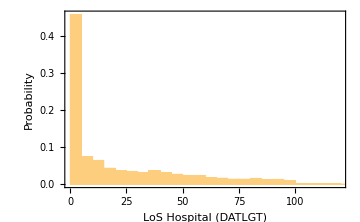
```mathematica
-Graphics-(*MG1*)
```

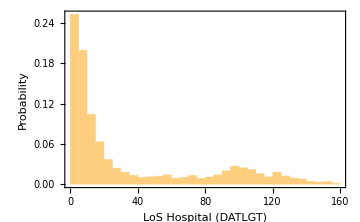
```mathematica
-Graphics-(*MG3*)
```

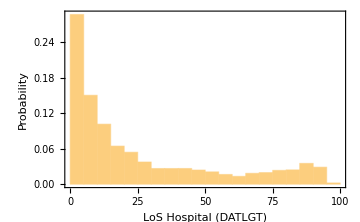
```mathematica
-Graphics- (*MG4*)
```

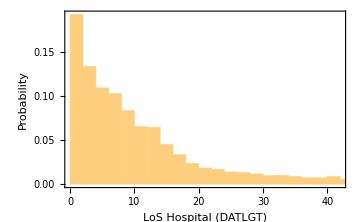
```mathematica
-Graphics- (*MG5*)
```

```mathematica
Length/@{DATAD,DATLGT} (*They have the same length due to DATDS is gotten joining the discharge variables to the whole set of cases *)
```

{22768,22768}

```mathematica
(*******************************************************************************)
```

```mathematica
DATADh=newDate/@(DATAD/.""->"Missing");
DATADh[[1;;10]] (*Entra al hospital-camaHospital*)
DATDSh=newDate/@DATDS;
DATDSh[[1;;10]](*Se descarga por recuperación, muerte, o tranferencia a otro hosp*)
DATLGTh=day/@(DATLGT/.-""+"Missing"->"Missing");
DATLGTh[[1;;10]](*Tiempo ocupando una cama de hospital*)
```

<|2→15/03/2020,7→15/03/2020,12→15/03/2020,13→15/03/2020,14→15/03/2020,16→18/03/2020,19→15/03/2020,33→01/04/2020,57→16/03/2020,61→14/11/2020|>

<|2→23/03/2020,7→23/03/2020,12→25/03/2020,13→25/03/2020,14→18/03/2020,16→29/03/2020,19→18/03/2020,33→12/04/2020,57→29/03/2020,61→15/11/2020|>

<|2→8,7→8,12→10,13→10,14→3,16→11,19→3,33→11,57→10,61→1|>

#### UCI bed occupation data: DATADI/DATDSI/DATLGTI

```mathematica
(*********************************************)
```

```mathematica
DATADI=AssociationThread[casesEvaluated->(adUCI[#]&/@casesOutcomefechas)];(*Date of admission UCI*)
```

```mathematica
fUCIToCRd=AssociationThread[casesEvaluated->(fUCIToCR[#]&/@casesOutcomefechas)];
```

```mathematica
fUCIToFd=AssociationThread[casesEvaluated->(fUCIToF[#]&/@casesOutcomefechas)];
```

```mathematica
fUCIToHd=AssociationThread[casesEvaluated->(fUCIToH[#]&/@casesOutcomefechas)];
```

```mathematica
DATDSI=Join[cases,DeleteCases[fUCIToCRd,""],DeleteCases[fUCIToFd,""],DeleteCases[fUCIToHd,""]];(*Discharge from UCI*)
```

```mathematica
DATLGTI=DATDSI-DATADI(* Length of stay in UCI*);
```

```mathematica
DATLGTI["3046547"]
```

33 days

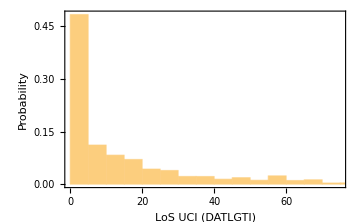

```mathematica
Histogram[Cases[DATLGTI,_Quantity],Automatic,"Probability",Frame->True,FrameLabel->{"LoS UCI (DATLGTI)","Probability"},ImageSize->Medium]
```

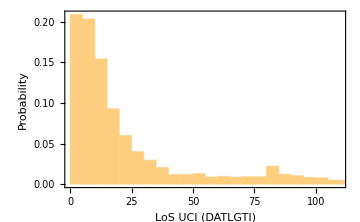
```mathematica
-Graphics-(*MG3*)
```

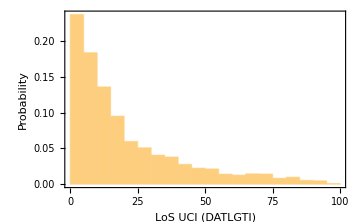
```mathematica
-Graphics-(*MG4*)
```

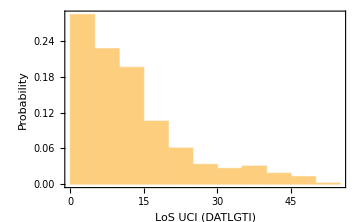
```mathematica
-Graphics-(*MG5*)
```

```mathematica
DATADIh=newDate/@(DATADI/.""->"Missing");
DATADIh[[1;;10]]
DATDSIh=newDate/@DATDSI;
DATDSIh[[1;;10]]
DATLGTIh=day/@(DATLGTI/.-""+"Missing"->"Missing");DATLGTIh[[1;;10]]
```

<|2→Missing,7→Missing,12→Missing,13→Missing,14→Missing,16→Missing,19→Missing,33→Missing,57→26/03/2020,61→Missing|>

<|2→Missing,7→Missing,12→Missing,13→Missing,14→Missing,16→Missing,19→Missing,33→Missing,57→29/03/2020,61→Missing|>

<|2→Missing,7→Missing,12→Missing,13→Missing,14→Missing,16→Missing,19→Missing,33→Missing,57→3,61→Missing|>

#### Calculating Yes/No for Admission: DSXHO / DSXIC

```mathematica
DSXHO=DATAD/.{""->"No",DateObject[___]->"Yes"};
```

```mathematica
DSXIC=DATADI/.{""->"No",DateObject[___]->"Yes"};
```

```mathematica
DSXHOh=DSXHO;DSXHOh[[1;;10]]
DSXICh=DSXIC;DSXICh[[1;;10]]
```

<|2→Yes,7→Yes,12→Yes,13→Yes,14→Yes,16→Yes,19→Yes,33→Yes,57→Yes,61→Yes|>

<|2→No,7→No,12→No,13→No,14→No,16→No,19→No,33→No,57→Yes,61→No|>

```mathematica
Length/@{DSXHO,DSXIC}
```

{22768,22768}

#### Calculating DSXOS/DATOS

```mathematica
fallecidos=AssociationThread[casesEvaluated->(estFallecido[#]&/@casesOutcomefechas)];
```

```mathematica
fallecidos["3046547"]
```

fallecido

```mathematica
fallecidos["4074598"]
```

Missing

```mathematica
recuperado=AssociationThread[casesEvaluated->(estRecuperado[#]&/@casesOutcomefechas)];
```

```mathematica
recuperado["3046547"]
```

Missing

```mathematica
recuperado["4074598"]
```

casa

```mathematica
DSXOS=Join[cases,DeleteCases[fallecidos,"Missing"],DeleteCases[recuperado,"Missing"]];(* Outcome status: Recovered/Deceased *)
```

```mathematica
DSXOS["3046547"]
```

fallecido

```mathematica
recuperado//DeleteDuplicates
```

<|2924537→casa,2924748→Missing|>

```mathematica
fallecidos//DeleteDuplicates
```

<|2924537→Missing,2924548→fallecido|>

```mathematica
casesOutcomefechas[[All,-1]]//DeleteDuplicates
```

{{2021-08-17,casa},{2021-08-17,fallecido}}

```mathematica
fallecidos[[1;;10]]
```

<|2924537→Missing,2924542→Missing,2924548→fallecido,2924550→Missing,2924551→fallecido,2924560→Missing,2924564→Missing,2924572→Missing,2924577→Missing,2924581→fallecido|>

```mathematica
DSXOS["caso1150"]
```

Missing[KeyAbsent,caso1150]

```mathematica
DSXOSh=(DSXOS/.{"recuperado"->"Recovered","casa"->"Recovered","fallecido"->"Deceased"});DSXOSh[[1;;10]]
```

<|2→Recovered,7→Recovered,12→Recovered,13→Recovered,14→Recovered,16→Recovered,19→Recovered,33→Recovered,57→Recovered,61→Recovered|>

```mathematica
Length[DSXOS]
```

22768

```mathematica
DSXOSh//DeleteDuplicates
```

<|2924537→Recovered,2924748→Deceased|>

```mathematica
(******************************************************************)
```

```mathematica
fallecidosD=AssociationThread[casesEvaluated->(feFallecido[#]&/@casesOutcomefechas)];
```

```mathematica
fallecidosD["3046547"]
```

Sat 19 Jun 2021

```mathematica
recuperadoD=AssociationThread[casesEvaluated->(feRecuperado[#]&/@casesOutcomefechas)];
```

```mathematica
recuperadoD["3046547"]
```

```mathematica
recuperadoD["4074598"]
```

Tue 13 Jul 2021

```mathematica
fallecidosD//Length
```

22768

```mathematica
recuperadoD//DeleteDuplicates
```

```mathematica
<|"2924537"->DateObject[{2021,7,20},"Day","Gregorian",-5.],"2924542"->DateObject[{2021,5,21},"Day","Gregorian",-5.],"2924548"->DateObject[{2021,5,13},"Day","Gregorian",-5.],"2924551"->"" ,"2924560"->DateObject[{2021,6,1},"Day","Gregorian",-5.],"2924564"->DateObject[{2021,5,20},"Day","Gregorian",-5.],"2924592"->DateObject[{2021,5,14},"Day","Gregorian",-5.],"2924613"->DateObject[{2021,6,12},"Day","Gregorian",-5.],"2924614"->DateObject[{2021,5,7},"Day","Gregorian",-5.],"2924628"->DateObject[{2021,5,18},"Day","Gregorian",-5.],"2924634"->DateObject[{2021,6,27},"Day","Gregorian",-5.],"2924669"->DateObject[{2021,6,23},"Day","Gregorian",-5.],"2924720"->DateObject[{2021,6,11},"Day","Gregorian",-5.],"2924766"->DateObject[{2021,5,10},"Day","Gregorian",-5.],"2924782"->DateObject[{2021,5,31},"Day","Gregorian",-5.],"2924824"->DateObject[{2021,5,16},"Day","Gregorian",-5.],"2924833"->DateObject[{2021,5,28},"Day","Gregorian",-5.],"2924854"->DateObject[{2021,6,25},"Day","Gregorian",-5.],"2924938"->DateObject[{2021,6,15},"Day","Gregorian",-5.],"2925039"->DateObject[{2021,5,24},"Day","Gregorian",-5.],"2925072"->DateObject[{2021,5,19},"Day","Gregorian",-5.],"2925130"->DateObject[{2021,7,7},"Day","Gregorian",-5.],"2925133"->DateObject[{2021,5,15},"Day","Gregorian",-5.],"2925141"->DateObject[{2021,6,19},"Day","Gregorian",-5.],"2925236"->DateObject[{2021,6,17},"Day","Gregorian",-5.],"2925287"->DateObject[{2021,6,4},"Day","Gregorian",-5.],"2925310"->DateObject[{2021,7,14},"Day","Gregorian",-5.],"2925684"->DateObject[{2021,6,2},"Day","Gregorian",-5.],"2925875"->DateObject[{2021,7,17},"Day","Gregorian",-5.],"2925920"->DateObject[{2021,5,11},"Day","Gregorian",-5.],"2925953"->DateObject[{2021,5,29},"Day","Gregorian",-5.],"2925999"->DateObject[{2021,5,22},"Day","Gregorian",-5.],"2926058"->DateObject[{2021,5,26},"Day","Gregorian",-5.],"2927673"->DateObject[{2021,8,7},"Day","Gregorian",-5.],"2927968"->DateObject[{2021,6,8},"Day","Gregorian",-5.],"2928326"->DateObject[{2021,7,26},"Day","Gregorian",-5.],"2928336"->DateObject[{2021,5,27},"Day","Gregorian",-5.],"2928392"->DateObject[{2021,8,6},"Day","Gregorian",-5.],"2928614"->DateObject[{2021,6,18},"Day","Gregorian",-5.],"2928653"->DateObject[{2021,8,1},"Day","Gregorian",-5.],"2929149"->DateObject[{2021,7,29},"Day","Gregorian",-5.],"2930171"->DateObject[{2021,8,8},"Day","Gregorian",-5.],"2930172"->DateObject[{2021,5,12},"Day","Gregorian",-5.],"2930387"->DateObject[{2021,8,3},"Day","Gregorian",-5.],"2930644"->DateObject[{2021,8,12},"Day","Gregorian",-5.],"2930906"->DateObject[{2021,6,16},"Day","Gregorian",-5.],"2930993"->DateObject[{2021,5,25},"Day","Gregorian",-5.],"2931055"->DateObject[{2021,6,3},"Day","Gregorian",-5.],"2931193"->DateObject[{2021,6,9},"Day","Gregorian",-5.],"2931297"->DateObject[{2021,5,23},"Day","Gregorian",-5.],"2931340"->DateObject[{2021,6,5},"Day","Gregorian",-5.],"2931402"->DateObject[{2021,5,17},"Day","Gregorian",-5.],"2931693"->DateObject[{2021,6,20},"Day","Gregorian",-5.],"2932982"->DateObject[{2021,7,9},"Day","Gregorian",-5.],"2933163"->DateObject[{2021,6,30},"Day","Gregorian",-5.],"2933342"->DateObject[{2021,6,26},"Day","Gregorian",-5.],"2933549"->DateObject[{2021,6,21},"Day","Gregorian",-5.],"2934183"->DateObject[{2021,7,30},"Day","Gregorian",-5.],"2934736"->DateObject[{2021,7,15},"Day","Gregorian",-5.],"2934746"->DateObject[{2021,7,18},"Day","Gregorian",-5.],"2935060"->DateObject[{2021,7,28},"Day","Gregorian",-5.],"2936556"->DateObject[{2021,6,7},"Day","Gregorian",-5.],"2938883"->DateObject[{2021,7,16},"Day","Gregorian",-5.],"2939199"->DateObject[{2021,7,5},"Day","Gregorian",-5.],"2939217"->DateObject[{2021,7,13},"Day","Gregorian",-5.],"2939884"->DateObject[{2021,7,21},"Day","Gregorian",-5.],"2940248"->DateObject[{2021,7,10},"Day","Gregorian",-5.],"2940292"->DateObject[{2021,7,8},"Day","Gregorian",-5.],"2941128"->DateObject[{2021,6,28},"Day","Gregorian",-5.],"2941156"->DateObject[{2021,7,22},"Day","Gregorian",-5.],"2941174"->DateObject[{2021,7,2},"Day","Gregorian",-5.],"2941277"->DateObject[{2021,6,13},"Day","Gregorian",-5.],"2943360"->DateObject[{2021,6,14},"Day","Gregorian",-5.],"2945877"->DateObject[{2021,7,3},"Day","Gregorian",-5.],"2948781"->DateObject[{2021,8,4},"Day","Gregorian",-5.],"2949113"->DateObject[{2021,6,6},"Day","Gregorian",-5.],"2950049"->DateObject[{2021,7,23},"Day","Gregorian",-5.],"2950476"->DateObject[{2021,7,11},"Day","Gregorian",-5.],"2951178"->DateObject[{2021,7,19},"Day","Gregorian",-5.],"2951854"->DateObject[{2021,7,27},"Day","Gregorian",-5.],"2953435"->DateObject[{2021,7,25},"Day","Gregorian",-5.],"2956922"->DateObject[{2021,7,12},"Day","Gregorian",-5.],"2957185"->DateObject[{2021,6,22},"Day","Gregorian",-5.],"2958325"->DateObject[{2021,7,24},"Day","Gregorian",-5.],"2961644"->DateObject[{2021,7,1},"Day","Gregorian",-5.],"2986311"->DateObject[{2021,8,11},"Day","Gregorian",-5.],"3014115"->DateObject[{2021,6,10},"Day","Gregorian",-5.],"3016999"->DateObject[{2021,8,17},"Day","Gregorian",-5.],"3023164"->DateObject[{2021,7,4},"Day","Gregorian",-5.],"3031648"->DateObject[{2021,6,29},"Day","Gregorian",-5.],"3033476"->DateObject[{2021,8,13},"Day","Gregorian",-5.],"3069224"->DateObject[{2021,8,14},"Day","Gregorian",-5.],"3075156"->DateObject[{2021,8,2},"Day","Gregorian",-5.],"3127136"->DateObject[{2021,6,24},"Day","Gregorian",-5.],"3165471"->DateObject[{2021,8,16},"Day","Gregorian",-5.],"3177892"->DateObject[{2021,8,15},"Day","Gregorian",-5.],"3283062"->DateObject[{2021,8,5},"Day","Gregorian",-5.]|>
```

```mathematica
fallecidosD[[1;;6]]
```

<|2924537→,2924542→,2924548→Tue 1 Jun 2021,2924550→,2924551→Fri 21 May 2021,2924560→|>

```mathematica
DATOS=Join[cases,DeleteCases[fallecidosD,""],DeleteCases[recuperadoD,""]];(* Outcome status: Recovered/Deceased *)
```

```mathematica
DATOSh=newDate/@DATOS;DATOSh[[100;;110]]
```

<|574→15/04/2020,579→15/04/2020,583→12/04/2020,586→19/04/2020,587→15/11/2020,591→15/11/2020,592→29/03/2020,594→05/09/2020,606→02/04/2020,610→10/04/2020,612→15/04/2020|>

```mathematica
Length[DATOSh]
```

7132

#### Fusion of the variables

```mathematica
(* Estoy poniendo Missing cuando no hay datos porque no esta en la base de datos quiza porque no ingresa a UCI o Hopsital o porque no se reportó el dato*)
```

```mathematica
dataBase={{"ID","DATAD","DATADI","DATDSI","DATDS","DATLGT","DATLGTI","DSXHO","DSXIC","DSXOS","DATOS"},Sequence@@Transpose[{cases//Keys,DATADh//Values,DATADIh//Values,DATDSIh//Values,DATDSh//Values,DATLGTh//Values,DATLGTIh//Values,DSXHOh//Values,DSXICh//Values,DSXOSh//Values,DATOSh//Values}]};
```

```mathematica
dataBase//Length
```

22769

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBase2021-G1.csv",dataBase,"CSV"];
```

```mathematica
(* dataBase2021-2.csv Esta base de datos se obtiene con la matrizM4 y es el masterG4 *)
```

```mathematica
Clear[day]
```

```mathematica
day["Missing"]:="Missing"
day[quantity_/;Head[quantity]==Quantity]:=QuantityMagnitude[quantity]
```

### Reviewing the final database

#### G1

```mathematica
dataBase=Import["/home/lina/Documents/UnCover/datos_INS/dataBase2021-G1.csv"];
```

```mathematica
dataBase//Length
```

22769

```mathematica
dataBase[[{1,Sequence@@RandomInteger[{2,10000},10]}]]//Grid
```

ID | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
2075281 | Missing | 29/01/2021 | 04/02/2021 | 04/02/2021 | Missing | 6 | No | Yes | Recovered | 04/02/2021
2148660 | 13/02/2021 | Missing | Missing | 17/02/2021 | 4 | Missing | Yes | No | Recovered | 17/02/2021
2119462 | 24/02/2021 | Missing | Missing | 04/03/2021 | 8 | Missing | Yes | No | Recovered | 04/03/2021
1983678 | Missing | 01/03/2021 | 12/03/2021 | 12/03/2021 | Missing | 11 | No | Yes | Recovered | 12/03/2021
2109996 | 02/02/2021 | Missing | Missing | 29/05/2021 | 116 | Missing | Yes | No | Recovered | 29/05/2021
1956975 | 29/01/2021 | Missing | Missing | 05/05/2021 | 96 | Missing | Yes | No | Recovered | 05/05/2021
2053032 | 08/02/2021 | Missing | Missing | 10/02/2021 | 2 | Missing | Yes | No | Recovered | 10/02/2021
1962262 | 27/01/2021 | Missing | Missing | 03/02/2021 | 7 | Missing | Yes | No | Deceased | 03/02/2021
1958685 | 21/01/2021 | Missing | Missing | 08/05/2021 | 107 | Missing | Yes | No | Recovered | 08/05/2021
1975270 | 22/01/2021 | Missing | Missing | 09/05/2021 | 107 | Missing | Yes | No | Recovered | 09/05/2021

```mathematica
dataBase[[17,{5,-1}]]
```

{18/04/2020,25/03/2020}

```mathematica
Position[MapThread[ToExpression[StringTake[#1,2]]-ToExpression[StringTake[#2,2]]&,{dataBase[[2;;,5]],dataBase[[2;;,-1]]}],x_/;x!=0]
```

{{16},{31},{40},{73},{77},{85},{110},{112},{118},{119},{139},{142},{148},{164},{168},{188},{201},{206},{210},{212},{213},{218},{227},{228},{344},{371},{377},{387},{438},{491},{542},{677},{838},{858},{1102},{1127},{1131},{1144},{1154},{1163},{1178},{1179},{1192},{1267},{1280},{1293},{1315},{1343},{1351},{1381},{1406},{1409},{1442},{1453},{1485},{1510},{1524},{1564},{1581},{1585},{1588},{1590},{1595},{1640},{1641},{1665},{1675},{1704},{1756},{1770},{1785},{1791},{1818},{1819},{1844,1},{1844,2,1},{1883},{1890},{1896},{1931},{1933},{1937},{1958},{1967},{1981},{1985},{2010},{2029},{2046},{2065},{2066},{2085},{2091},{2092},{2093},{2097},{2113},{2115},{2124},{2136},{2149},{2172},{2180},{2185},{2211},{2227},{2238},{2240},{2258},{2272},{2303},{2311},{2335},{2349},{2351},{2360},{2361},{2369},{2373},{2375},{2389},{2405},{2411},{2453},{2462},{2493},{2497},{2520},{2536},{2541},{2549},{2574},{2613},{2618},{2626},{2632},{2642},{2653},{2660},{2676},{2694},{2743},{2762},{2764},{2766},{2788},{2819},{2825},{2833},{2840},{2870},{2894},{2913},{2915},{2918},{2922},{2931},{2944},{2971},{2976},{2994},{3003},{3012},{3044},{3049},{3059},{3066},{3082},{3098},{3100},{3105},{3119},{3123},{3125},{3171},{3174},{3176},{3179},{3191},{3196},{3204},{3210},{3221},{3232},{3248},{3265},{3269},{3288},{3294,1},{3294,2,1},{3409},{3595},{3608},{3613},{3676},{3715},{3746},{3748},{3788},{3800},{3830},{3831},{3874},{3962},{3994},{3997},{4007},{4020},{4047},{4059},{4120},{4289},{4310},{4333},{4335},{4350},{4364},{4408},{4417},{4445},{4493},{4502},{4518},{4563},{4626},{4643},{4659},{4684},{4689},{4752},{4762},{4768},{4776},{4792},{4858},{4869},{4888},{4890},{4968},{4969},{5047},{5056},{5083},{5110},{5133},{5153},{5171},{5193},{5232},{5241},{5297},{5340},{5342},{5406},{5408},{5509},{5562},{5629},{5677},{5685},{5697},{5711},{5733},{5862},{5876},{5886},{6160},{6311},{6382},{6396},{6476},{6599},{6696},{6745},{6790},{6974},{7103},{7299},{7645},{7654},{7662},{7968},{8057},{8077},{8189},{8295},{8311},{8329},{8433},{8599},{8678},{8692,1},{8692,2,1},{8762},{8890},{8975},{9074},{9165},{9242},{9270},{9287},{9291},{9411},{9432},{9498},{9561},{9581},{9598},{9714},{9804},{10070},{10109},{10124},{10144},{10165},{10270},{10289},{10447},{10519},{10559},{10587},{10765},{10873},{10898},{11054},{11093},{11094},{11099},{11152},{11189},{11319},{11351},{11399},{11426},{11464},{11531},{11781},{11853},{11929},{12180},{12302},{12310},{12343},{12355},{12436},{12505},{12848},{12894},{12897},{12911},{12946},{12992},{12999},{13196},{13258,1},{13258,2,1},{13319},{13346},{13616},{13799},{13846},{13865},{13934},{14015},{14102},{14108},{14111},{14245},{14404},{14406},{14452},{14460},{14511},{14586},{14624},{14651},{14790},{14840},{15036},{15172},{15308},{15454},{15511},{15574},{15761},{15807},{15856},{15962},{15974},{15975},{16005},{16007},{16070},{16096},{16188},{16191},{16226},{16242},{16283},{16309},{16312},{16544},{16577},{16607},{16619},{16635},{16660},{16743},{16773},{16890},{16989},{17064},{17110},{17164},{17219},{17232},{17340},{17447},{17469},{17481},{17545},{17546},{17554},{17643},{17695},{17809},{17850},{17861},{17906},{17963},{17995},{18177},{18190},{18214},{18387},{18513},{18557},{18740},{18864},{18899},{18925},{18940},{19009},{19103},{19112},{19118},{19150},{19191},{19200},{19238},{19245},{19277},{19278},{19351},{19391},{19396},{19407},{19527},{19566},{19628},{19644},{19693},{19754},{19763},{19782},{19827},{19867},{20035},{20041},{20042},{20222},{20251},{20335},{20422},{20455},{20530},{20598},{20614},{20663},{20671},{20723},{20785},{20840},{20926},{20986},{21052},{21158},{21213},{21223},{21281},{21287},{21314},{21326},{21370},{21431},{21537},{21566},{21571},{21742},{21774},{21886},{21928},{21934},{21942},{21950},{22015},{22033},{22088},{22138},{22167},{22174},{22217},{22272},{22331},{22334},{22361},{22387},{22393},{22397},{22407},{22433},{22443},{22452},{22574},{22637},{22645},{22686},{22692},{22711},{22834},{22887},{22905},{23002},{23012},{23018},{23021},{23047},{23066},{23160},{23177},{23187},{23204},{23240},{23255},{23277},{23287},{23304},{23393},{23472},{23473},{23534},{23541},{23587},{23606},{23673},{23674},{23724},{23818},{23821},{23834},{23838},{23840},{23859},{23863},{23907},{23924},{24025},{24064},{24084},{24115},{24133},{24136},{24162},{24163},{24172},{24175},{24194},{24208},{24262},{24273},{24387},{24432},{24509},{24576},{24605},{24636},{24637},{24659},{24664},{24670},{24679},{24720},{24771},{24802},{24842},{25170},{25173},{25214},{25250},{25256},{25279},{25310},{25346},{25365},{25404},{25432},{25444},{25550},{25566},{25600},{25744},{25825},{25878},{25946},{25953},{25965},{26001},{26002},{26009},{26053},{26127},{26130},{26137},{26154},{26170},{26172},{26182},{26293},{26298},{26307},{26308},{26310},{26345},{26404},{26432},{26464},{26492},{26495},{26558},{26577},{26790},{26903},{26924},{26925},{26957},{26960},{26964},{27086},{27091},{27106},{27120},{27154},{27161},{27277},{27287},{27309},{27340},{27362},{27391},{27412},{27421},{27476},{27486},{27516},{27546},{27637},{27668},{27684},{27687},{27696},{27700},{27703},{27712},{27735},{27757},{27776},{27781},{27802},{27807},{27813},{27840},{27850},{27912},{27921},{27945},{27948},{28030},{28049},{28084},{28111},{28155},{28165},{28173},{28207},{28261},{28395},{28424},{28429},{28440},{28453},{28489},{28518},{28564},{28571},{28594},{28624},{28696},{28725},{28778},{28784},{28813},{28857},{28922},{28949},{28958},{28961},{28964},{28991},{28993},{28999},{29001},{29014},{29033},{29047},{29075},{29086},{29089},{29092},{29095},{29114},{29117},{29122},{29155},{29160},{29178},{29183},{29184},{29193},{29224},{29242},{29257},{29267,1},{29267,2,1},{29273},{29280},{29284},{29326},{29425},{29449},{29505},{29556},{29561},{29569},{29595},{29700},{29731},{29741},{29761},{29767},{29773},{29777},{29794},{29801},{29824},{29826},{29863},{29869},{29908},{29944},{29983},{30020},{30051},{30056},{30060},{30062},{30072},{30103},{30126},{30194},{30218},{30259},{30275},{30392},{30407},{30430},{30461},{30669},{30681},{30699},{30715},{30729},{30759},{30783},{30791},{30799},{30807},{30812},{30834,1},{30834,2,1},{30876},{30879},{30886},{31046},{31069},{31101},{31164},{31181},{31254},{31259},{31299},{31343},{31363},{31436},{31437},{31483},{31487},{31565},{31602},{31677},{31681},{31700},{31718},{31747},{31765},{31777},{31827},{31871},{31884},{31885},{31929},{31930},{31946},{31967},{31991},{32006},{32041},{32050},{32091},{32276},{32322},{32330},{32358},{32360},{32365},{32367},{32391},{32487},{32514},{32541},{32563},{32610},{32643},{32732},{32879},{32882},{32905},{32962},{32982},{32984},{32995},{33017},{33054},{33095},{33108},{33110},{33122},{33188},{33228},{33287},{33291},{33328},{33346},{33380},{33383},{33399},{33416},{33450},{33462},{33484},{33611},{33714},{33772},{33827},{33851},{33858},{33882},{33936},{33938},{33944},{33989},{34064},{34152},{34165},{34172},{34202},{34228},{34247},{34281},{34282},{34344},{34378},{34396},{34427},{34461},{34471},{34499},{34508},{34509},{34560},{34565},{34586},{34661},{34695},{34737},{34770},{34774},{34779},{34792},{34816},{34817},{34822},{34826},{34834},{34932},{34937},{34942},{34995},{34998},{34999},{35023},{35047},{35048},{35049},{35082},{35095},{35097},{35109},{35110},{35148},{35167},{35188},{35196},{35210},{35225},{35237},{35250},{35290},{35313},{35335},{35401},{35404},{35408},{35418},{35421},{35440},{35460},{35467},{35479},{35557},{35624},{35672},{35691},{35697},{35747},{35790},{35793},{35804},{35855},{35880},{35901},{35921},{35922},{35954},{35989},{36038},{36097},{36170},{36197},{36324},{36351},{36359},{36366},{36445},{36449},{36460},{36478},{36487},{36511},{36542},{36598},{36647},{36648},{36660},{36676},{36719},{36726},{36752},{36791},{36877},{36945},{36961},{37084},{37108},{37126},{37146},{37164},{37176},{37227},{37249},{37258},{37272},{37279},{37306},{37330},{37379},{37408,1},{37408,2,1},{37414},{37444,1},{37444,2,1},{37493},{37558},{37650},{37666},{37776},{37824},{37882},{37899},{37998},{37999},{38021},{38051},{38070},{38081},{38087},{38088},{38111},{38182},{38260},{38346},{38364},{38365},{38371},{38395},{38423},{38458},{38465},{38497},{38519},{38584},{38707},{38768},{38784},{38794},{38830},{38864},{38882},{38889},{38893},{39082},{39112},{39150},{39166},{39167},{39210},{39237},{39315},{39361},{39416},{39428},{39430},{39485},{39560},{39573},{39658},{39673},{39705},{39727},{39739},{39767},{39778},{39784},{39915},{39936},{39939},{40037},{40043},{40050},{40138},{40140},{40169},{40222},{40274},{40314},{40320},{40534},{40543},{40558},{40569},{40579},{40583},{40624},{40640},{40642},{40738},{40768},{40771},{40815},{40820},{40981},{41119},{41345},{41450},{41521},{41524},{41544},{41635},{41717},{41757},{41761},{41774},{41870},{41895},{41966},{42048},{42157},{42189},{42211},{42254},{42271},{42362},{42772},{43008},{43083},{43167},{43296},{43347},{43488},{43626},{43630},{43637},{43675},{43688},{43689},{43751},{43753},{43910},{44013},{44220},{44289},{44509},{44514},{44537},{44564},{44580},{44661},{44712},{44742},{44845},{44858},{44891},{45000},{45011},{45053},{45070},{45151},{45247},{45250},{45276},{45302},{45411},{45543},{45584},{45621},{45698},{45704},{45850},{45876},{46195},{46311},{46317},{46318},{46337},{46382},{46440},{46470},{46523},{46529},{46633},{46728},{46839},{47075},{47078},{47148},{47156},{47223},{47351},{47379},{47395},{47408},{47436},{47908},{48031},{48153},{48157},{48168},{48186},{48283},{48339},{48361},{48365},{48460},{48489},{48521},{48618},{48674},{48739},{48803},{48806},{49077},{49176},{49237},{49253},{49315},{49322},{49472},{49477},{49829},{49936},{49958},{50015},{50288},{50299},{50309},{50391},{50417},{50459},{50482},{50788},{50827},{50896},{50963},{50980},{50996},{51131},{51249},{51389},{51579},{51590},{51674},{51717},{51735},{51742},{51847},{51881},{51914},{51942},{51959},{51995},{51996},{52079},{52150},{52300},{52325},{52417},{52436},{52535},{52572},{52602},{52641},{52654},{53021},{53079},{53249},{53554},{53671},{53683},{53741},{53765},{53880},{54017},{54108},{54131},{54161},{54216},{54220},{54245},{54279},{54289},{54361},{54372},{54385},{54435},{54520},{54525},{54594},{54636},{54684},{54689},{54730},{54808},{54813},{54939},{55012},{55076},{55185},{55243},{55283},{55480},{55518},{55588},{55680},{55898},{56015},{56017},{56026},{56098},{56251},{56262},{56327},{56328},{56397},{56461},{56517},{56587},{56662},{56737},{56743},{56799},{56818},{56837},{56874},{56875},{56941},{56944},{56971},{57213},{57236},{57361},{57364},{57474},{57761},{57764},{57789},{57970},{58141,1},{58141,2,1},{58149},{58175},{58182},{58204},{58222},{58258},{58281},{58286},{58324},{58411},{58412},{58414},{58597},{58656},{58679},{58749},{58986},{59012},{59054},{59060},{59073},{59074},{59164},{59171},{59194},{59216},{59239},{59421},{59682},{59735},{59765},{59783},{59871},{59881},{59911},{59951},{59998},{60004},{60042},{60064},{60358},{60377},{60497},{60517},{60537},{60616},{60646},{60806},{60916},{60948},{60959},{61029},{61121},{61128},{61133},{61142},{61274},{61370},{61406},{61454},{61497},{61531},{61532},{61556},{61606},{61665},{61689},{61756},{61789},{61917},{61950},{61967},{62084},{62159},{62243},{62315},{62316},{62364},{62392},{62406},{62451},{62455},{62456},{62476},{62549},{62581},{62675},{62694},{63252},{63268},{63269},{63425},{63665},{63673},{63738},{63804},{63896},{64022},{64165},{64335},{64339},{64548},{64565},{64605},{64617},{64618},{64627},{64710},{64744},{64787},{64857},{64967},{65337},{65350},{65671},{65754},{65905},{65972},{66046},{66116},{66182},{66192},{66242},{66285},{66323},{66441},{66478},{66505},{66513,1},{66513,2,1},{66552},{66618},{66674},{66726},{67019},{67092},{67198},{67206},{67243},{67269},{67320},{67335},{67451},{67584},{67688},{67710},{67745},{67800},{67820},{67838},{67851},{67933},{67978},{67979},{67990},{68053},{68191},{68217},{68254},{68259},{68265},{68406},{68441},{68653},{68669},{68687},{68688},{68750},{68830},{68876},{68895},{68936},{69122},{69177},{69353},{69387},{69452},{69504},{69703},{69762},{69787},{69894},{70050},{70117},{70181},{70267},{70305},{70352},{70396},{70412},{70458},{70485},{70503},{70616},{70642},{70650},{70683},{70706},{70811},{70823},{70910,1},{70910,2,1},{71014},{71058},{71083},{71159},{71219},{71281},{71303},{71404},{71459},{71501},{71640},{71728},{71738},{71771},{72212},{72232},{72350},{72468},{72569},{72652},{72781},{72791},{72796},{72819},{72846},{72848},{72972},{73183},{73191},{73256},{73319},{73458},{73473},{73536},{73622},{73669},{73775},{73830},{73927},{74001},{74018},{74063},{74077},{74111},{74126},{74487},{74495},{74539},{74543},{74718},{74758},{74949},{74958},{74963},{74966},{74973},{75077},{75106},{75109},{75111},{75112},{75178},{75192},{75237},{75359},{75379},{75386},{75391},{75446},{75514},{75585},{75588},{75612},{75813},{75845},{76138},{76224},{76238},{76339},{76508},{76519},{76541},{76589},{76699},{76898},{76901},{76940},{76975},{76978},{77027},{77035},{77088},{77170},{77377},{77379},{77381},{77426},{77531},{77597},{77710},{77823},{77829},{77851},{77862},{77907},{78089},{78155},{78159},{78198},{78238},{78241},{78365},{78408},{78433},{78472},{78474},{78511},{78516},{78530},{78542},{78735},{78770},{78798},{78876},{78882},{78901},{78944},{78962},{79016},{79228},{79367},{79446},{79448},{79478},{79583},{79641},{79662},{79694},{79786},{79791},{80106},{80223,1},{80223,2,1},{80251},{80286},{80338},{80498},{80516},{80524},{80536},{80705},{80722},{80756},{80821},{80855},{80885},{80913},{80925},{80998},{81068},{81077},{81220},{81229},{81293},{81302},{81362},{81363},{81382},{81479},{81503},{81574},{81619},{81719},{81894},{81896},{81920},{81964},{82071},{82075},{82111},{82174},{82193},{82251},{82256},{82358},{82371},{82397},{82400},{82417},{82439},{82440},{82489},{82497},{82544},{82577},{82605},{82610},{82739},{82740},{82861},{82880},{82906},{82961},{82998},{83037},{83077},{83088},{83128},{83134},{83164},{83198},{83210},{83251},{83253},{83286},{83302},{83307},{83317},{83345},{83390},{83406},{83503},{83573},{83609},{83686},{83694},{83736},{83742},{83788},{83814,1},{83814,2,1},{83830},{84083},{84150},{84172},{84402},{84406},{84458},{84485},{84494},{84505},{84507},{84522},{84543},{84547},{84548},{84549},{84554},{84571},{84764},{84836},{85001},{85066},{85089},{85263},{85279},{85314},{85349},{85476},{85491},{85497},{85592},{85616},{85620},{85624},{85678},{85718},{85738},{85820},{85893},{85951},{85960},{85970},{85973},{86004},{86028},{86096},{86128},{86326},{86349},{86378},{86412},{86471},{86624},{86632},{86635},{86636},{86757},{86826},{86829},{86886},{86974},{87008},{87019},{87022},{87048},{87107},{87128},{87139},{87207},{87212},{87220},{87226},{87400},{87674},{87718},{87803},{87862},{87967},{87985},{88003},{88050},{88076},{88137},{88141},{88156},{88226},{88254},{88274},{88284},{88294},{88312},{88324},{88328},{88344},{88357},{88359},{88360},{88388},{88395},{88402},{88414},{88426},{88441},{88451},{88461},{88474},{88475},{88486},{88504},{88594},{88597},{88638},{88641},{88675},{88723},{88731},{88732},{88734},{88801},{88956},{88962},{88963},{88971},{89154},{89260},{89263},{89360},{89451},{89497},{89522},{89542},{89571},{89688,1},{89688,2,1},{89692},{89801},{89898},{89917},{89948},{90003},{90074},{90104},{90113},{90115},{90119},{90312},{90317},{90336},{90357},{90400},{90422},{90584},{90650},{90720},{90740},{90743},{90923},{91025},{91031},{91040},{91055},{91122},{91128},{91149},{91181},{91204},{91208},{91288},{91293},{91418},{91516},{91560},{91573},{91741},{91780},{91785},{91794},{91816},{91842},{91913},{92037},{92068},{92139},{92161},{92442},{92461},{92468},{92490},{92509},{92546},{92568},{92569},{92598},{92631},{92661},{92701},{92748},{92788},{92796},{92875},{92878},{92894},{93092},{93128},{93166},{93171},{93235},{93263},{93344},{93381},{93404},{93431},{93466},{93468},{93474},{93493},{93582},{93590},{93594},{93646},{93652},{93680},{93691},{93696},{93741},{93766},{93826},{93836},{93845},{94031},{94050},{94073},{94076},{94094},{94107},{94111},{94136},{94153},{94177},{94318},{94355},{94368},{94379},{94394},{94451},{94545},{94580},{94610},{94627},{94631},{94718},{94766},{94940},{94979},{94981},{94988},{94992},{95012},{95024},{95065},{95153},{95331},{95493},{95570},{95582},{95585},{95656},{95678},{95682},{95688},{95723},{95739},{95752},{95819},{95857},{95877},{95896},{95907},{95928},{95947},{95972},{95991},{96123},{96167},{96168},{96329},{96334},{96412},{96454},{96494},{96496},{96583},{96693},{96704},{96706},{96708},{96735},{96780},{96839},{96867},{96930},{96936},{97042},{97123},{97125},{97142},{97150},{97186},{97293},{97397},{97537},{97581},{97588},{97590},{97604},{97729},{97757},{97781},{97847},{97902},{97915},{97925},{97978},{98057},{98065},{98073},{98088},{98124},{98126},{98129},{98144},{98166},{98211},{98278},{98283},{98290},{98341},{98443},{98481},{98532},{98630},{98651},{98680},{98682},{98748},{98761},{98785},{98858},{98898},{98903},{98939},{98955},{99051},{99129},{99164},{99169},{99311},{99326},{99329},{99364},{99406},{99457},{99465},{99474},{99519},{99548},{99585},{99587},{99620},{99675},{99711},{99723},{99753},{99761},{99796},{99838},{99865},{99867},{99879},{100032},{100077},{100089},{100109},{100172},{100175},{100194},{100207},{100358},{100439},{100473},{100496},{100498},{100530},{100550},{100590},{100595},{100611},{100665},{100722},{100762},{100769},{100788},{100791},{100910},{100925},{100943},{100960},{100987},{101038},{101042},{101085},{101118},{101120},{101192},{101245},{101266},{101293},{101301},{101331},{101352},{101369},{101378},{101388},{101509},{101600},{101632},{101645},{101683},{101737},{101738},{101779},{101797},{101817},{101916},{101949},{101984},{101996},{102009},{102027},{102028},{102114},{102140},{102180},{102213},{102242},{102251},{102252},{102255},{102273},{102387},{102425},{102491},{102503},{102543},{102674},{102780},{102786},{102857},{102872},{102913},{102998},{103021},{103049},{103063},{103098},{103100},{103130},{103146},{103149},{103179},{103191},{103192},{103209},{103245},{103270},{103344},{103369},{103439},{103486},{103506},{103548},{103589},{103625},{103629},{103661},{103671},{103673},{103696},{103781},{103865},{103974},{104035},{104040},{104083},{104198},{104202},{104289},{104328},{104375},{104432},{104443},{104445},{104465},{104478},{104499},{104540},{104644},{104672},{104707},{104730},{104763},{104776},{104777},{104784},{104790},{104791},{104798},{104823},{104837},{104851},{104882},{104912},{104916},{104929},{104936},{104997},{105004},{105041},{105092},{105283},{105287},{105319},{105375},{105417},{105480},{105536},{105581},{105599},{105662},{105740},{105758},{105844},{105854},{105865},{105917},{105942},{105948},{105949},{105967},{106057},{106080},{106153},{106167},{106177},{106197},{106203},{106226},{106239},{106241},{106374},{106377},{106399},{106405},{106425},{106462},{106470},{106536},{106544},{106555},{106611},{106656},{106713},{106769},{106824},{106845},{106882},{106888},{106891},{106902},{106903},{106916},{106923},{106994},{107030},{107037},{107047},{107051},{107052},{107093},{107129},{107142},{107242},{107259},{107261},{107295},{107301},{107314},{107317},{107329},{107348},{107381},{107382},{107383},{107404},{107418},{107471},{107532},{107585},{107599},{107602},{107613},{107639},{107714},{107722},{107760},{107783},{107796},{107815},{107828},{107833},{107862}}

```mathematica
(****************************************++case 3046547 +1*)
```

```mathematica
Select[dataBase,#[[1]]=="1974507"&]
```

{{1974507,22/01/2021,Missing,Missing,24/01/2021,2,Missing,Yes,No,Deceased,24/01/2021}}

```mathematica
caso[[1]]
```

{fecha_hoy_casos,Caso,Fecha Not,Departamento,Departamento_nom,Ciudad_municipio,Ciudad_municipio_nom,Edad,unidad_medida,Sexo,Fuente_tipo_contagio,Ubicacion,Estado,Pais_viajo_1_cod,Pais_viajo_1_nom,Recuperado,Fecha_inicio_sintomas,Fecha_muerte,Fecha_diagnostico,Fecha_recuperado,Tipo_recuperacion,per_etn_,nom_grupo_}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-01-22.csv"];
```

```mathematica
caso[[1974507+1]]
```

{22/1/2021 0:00:00,19274547,18/1/2021 0:00:00,63,QUINDIO,63001,ARMENIA,81,1,M,En estudio,Hospital,Moderado,,,Activo,13/1/2021 0:00:00,,21/1/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-01-23.csv"];
```

```mathematica
caso2[[1974507+1]]
```

{22/1/2021 0:00:00,1974547,18/1/2021 0:00:00,63,QUINDIO,63001,ARMENIA,81,1,M,En estudio,Hospital,Moderado,,,Activo,13/1/2021 0:00:00,,21/1/2021 0:00:00,,,,}

#### G3

```mathematica
dataBase=Import["/home/lina/Documents/datos_INS/dataBase2021-G3.csv"];
```

```mathematica
dataBase//Length
```

22769

```mathematica
dataBase[[{1,Sequence@@RandomInteger[{2,10000},10]}]]//Grid
```

ID | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
2075281 | Missing | 29/01/2021 | 04/02/2021 | 04/02/2021 | Missing | 6 | No | Yes | Recovered | 04/02/2021
2148660 | 13/02/2021 | Missing | Missing | 17/02/2021 | 4 | Missing | Yes | No | Recovered | 17/02/2021
2119462 | 24/02/2021 | Missing | Missing | 04/03/2021 | 8 | Missing | Yes | No | Recovered | 04/03/2021
1983678 | Missing | 01/03/2021 | 12/03/2021 | 12/03/2021 | Missing | 11 | No | Yes | Recovered | 12/03/2021
2109996 | 02/02/2021 | Missing | Missing | 29/05/2021 | 116 | Missing | Yes | No | Recovered | 29/05/2021
1956975 | 29/01/2021 | Missing | Missing | 05/05/2021 | 96 | Missing | Yes | No | Recovered | 05/05/2021
2053032 | 08/02/2021 | Missing | Missing | 10/02/2021 | 2 | Missing | Yes | No | Recovered | 10/02/2021
1962262 | 27/01/2021 | Missing | Missing | 03/02/2021 | 7 | Missing | Yes | No | Deceased | 03/02/2021
1958685 | 21/01/2021 | Missing | Missing | 08/05/2021 | 107 | Missing | Yes | No | Recovered | 08/05/2021
1975270 | 22/01/2021 | Missing | Missing | 09/05/2021 | 107 | Missing | Yes | No | Recovered | 09/05/2021

```mathematica
(****************************************++case 3046547 +1*)
```

```mathematica
Select[dataBase,#[[1]]=="1974507"&]
```

{{1974507,22/01/2021,Missing,Missing,24/01/2021,2,Missing,Yes,No,Deceased,24/01/2021}}

```mathematica
caso[[1]]
```

{fecha_hoy_casos,Caso,Fecha Not,Departamento,Departamento_nom,Ciudad_municipio,Ciudad_municipio_nom,Edad,unidad_medida,Sexo,Fuente_tipo_contagio,Ubicacion,Estado,Pais_viajo_1_cod,Pais_viajo_1_nom,Recuperado,Fecha_inicio_sintomas,Fecha_muerte,Fecha_diagnostico,Fecha_recuperado,Tipo_recuperacion,per_etn_,nom_grupo_}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-01-22.csv"];
```

```mathematica
caso[[1974507+1]]
```

{22/1/2021 0:00:00,19274547,18/1/2021 0:00:00,63,QUINDIO,63001,ARMENIA,81,1,M,En estudio,Hospital,Moderado,,,Activo,13/1/2021 0:00:00,,21/1/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-01-23.csv"];
```

```mathematica
caso2[[1974507+1]]
```

{22/1/2021 0:00:00,1974547,18/1/2021 0:00:00,63,QUINDIO,63001,ARMENIA,81,1,M,En estudio,Hospital,Moderado,,,Activo,13/1/2021 0:00:00,,21/1/2021 0:00:00,,,,}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2021-01-24.csv"];
```

```mathematica
caso3[[1974507+1]]
```

{22/1/2021 0:00:00,1974547,18/1/2021 0:00:00,63,QUINDIO,63001,ARMENIA,81,1,M,En estudio,Fallecido,Fallecido,,,Fallecido,13/1/2021 0:00:00,24/1/2021 0:00:00,21/1/2021 0:00:00,,,,}

```mathematica
(*****************""2075281""+1*)
```

```mathematica
Select[dataBase,#[[1]]=="2075281"&]
```

{{2075281,Missing,29/01/2021,04/02/2021,04/02/2021,Missing,6,No,Yes,Recovered,04/02/2021}}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-01-29.csv"];
```

```mathematica
caso1[[2075281+1]]
```

{29/1/2021 0:00:00,2075321,7/1/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,73,1,F,En estudio,Hospital UCI,Grave,,,Activo,6/1/2021 0:00:00,,28/1/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-02-04.csv"];
```

```mathematica
caso2[[2075281+1]]
```

{29/1/2021 0:00:00,2075321,7/1/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,73,1,F,En estudio,Casa,Leve,,,Activo,6/1/2021 0:00:00,,28/1/2021 0:00:00,,,,}

#### G4

```mathematica
dataBase=Import["/home/lina/Documents/datos_INS/dataBase2021-G4.csv"];
```

```mathematica
dataBase//Length
```

22769

```mathematica
dataBase[[{1,Sequence@@RandomInteger[{2,10000},10]}]]//Grid
```

ID | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
3049172 | 31/05/2021 | Missing | Missing | 07/08/2021 | 68 | Missing | Yes | No | Recovered | 07/08/2021
3113122 | 16/05/2021 | Missing | Missing | 17/05/2021 | 1 | Missing | Yes | No | Deceased | 17/05/2021
3168320 | 31/05/2021 | Missing | Missing | 16/06/2021 | 16 | Missing | Yes | No | Deceased | 16/06/2021
3072835 | 14/05/2021 | Missing | Missing | 07/08/2021 | 85 | Missing | Yes | No | Recovered | 07/08/2021
3066005 | 22/05/2021 | Missing | Missing | 15/07/2021 | 54 | Missing | Yes | No | Recovered | 15/07/2021
2968287 | 12/05/2021 | Missing | Missing | 14/05/2021 | 2 | Missing | Yes | No | Deceased | 14/05/2021
3058665 | 13/05/2021 | Missing | Missing | 19/05/2021 | 6 | Missing | Yes | No | Recovered | 19/05/2021
3035071 | Missing | 25/05/2021 | 12/08/2021 | 12/08/2021 | Missing | 79 | No | Yes | Recovered | 12/08/2021
3004923 | 10/05/2021 | Missing | Missing | 21/05/2021 | 11 | Missing | Yes | No | Deceased | 21/05/2021
3166974 | 20/05/2021 | Missing | Missing | 29/05/2021 | 9 | Missing | Yes | No | Deceased | 29/05/2021

```mathematica
(****************************************++case 3046547 +1*)
```

```mathematica
Select[dataBase,#[[1]]=="3046547"&]
```

{{3046547,Missing,17/05/2021,19/06/2021,19/06/2021,Missing,33,No,Yes,Deceased,19/06/2021}}

```mathematica
caso[[1]]
```

{fecha_hoy_casos,Caso,Fecha Not,Departamento,Departamento_nom,Ciudad_municipio,Ciudad_municipio_nom,Edad,unidad_medida,Sexo,Fuente_tipo_contagio,Ubicacion,Estado,Pais_viajo_1_cod,Pais_viajo_1_nom,Recuperado,Fecha_inicio_sintomas,Fecha_muerte,Fecha_diagnostico,Fecha_recuperado,Tipo_recuperacion,per_etn_,nom_grupo_}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-05-16.csv"];
```

```mathematica
caso[[3046547+1]]
```

{12/5/2021 0:00:00,3046587,7/5/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,En estudio,Casa,Leve,,,Activo,6/5/2021 0:00:00,,11/5/2021 0:00:00,,,6,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-05-17.csv"];
```

```mathematica
caso2[[3046547+1]]
```

{12/5/2021 0:00:00,3046587,7/5/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,En estudio,Hospital UCI,Grave,,,Activo,6/5/2021 0:00:00,,11/5/2021 0:00:00,,,6,}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2021-06-18.csv"];
```

```mathematica
caso3[[3046547+1]]
```

{12/5/2021 0:00:00,3046587,7/5/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,En estudio,Hospital UCI,Grave,,,Activo,6/5/2021 0:00:00,,11/5/2021 0:00:00,,,6,}

```mathematica
caso4=Import["/home/lina/Documents/datos_INS/2021-06-19.csv"];
```

```mathematica
caso4[[3046547+1]]
```

{12/5/2021 0:00:00,3046587,7/5/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,En estudio,Fallecido,Fallecido,,,Fallecido,6/5/2021 0:00:00,18/6/2021 0:00:00,11/5/2021 0:00:00,,,6,}

```mathematica
(*****************"2965006"+1*)
```

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-05-07.csv"];
```

```mathematica
caso[[2965006+1]]
```

{7/5/2021 0:00:00,2965046,4/5/2021 0:00:00,68,SANTANDER,68001,BUCARAMANGA,89,1,M,En estudio,Hospital,Moderado,,,Activo,26/4/2021 0:00:00,,4/5/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-05-08.csv"];
```

```mathematica
caso2[[2965006+1]]
```

{7/5/2021 0:00:00,2965046,4/5/2021 0:00:00,68,SANTANDER,68001,BUCARAMANGA,89,1,M,En estudio,Fallecido,Fallecido,,,Fallecido,26/4/2021 0:00:00,5/5/2021 0:00:00,4/5/2021 0:00:00,,,,}

#### G5

```mathematica
dataBase=Import["/home/lina/Documents/UnCover/datos_INS/dataBase2021-G5.csv"];
```

```mathematica
dataBase//Length
```

10997

```mathematica
dataBase[[{1,Sequence@@RandomInteger[{2,10000},10]}]]//Grid
```

ID | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
4135972 | Missing | 28/06/2021 | 11/08/2021 | 11/08/2021 | Missing | 44 | No | Yes | Recovered | 11/08/2021
4112887 | Missing | 28/06/2021 | 11/08/2021 | 11/08/2021 | Missing | 44 | No | Yes | Recovered | 11/08/2021
4314811 | Missing | 07/07/2021 | 23/07/2021 | 23/07/2021 | Missing | 16 | No | Yes | Deceased | 23/07/2021
4538612 | 13/07/2021 | Missing | Missing | 15/07/2021 | 2 | Missing | Yes | No | Deceased | 15/07/2021
4528865 | 01/08/2021 | Missing | Missing | 14/08/2021 | 13 | Missing | Yes | No | Recovered | 14/08/2021
4231156 | Missing | 09/07/2021 | 21/07/2021 | 21/07/2021 | Missing | 12 | No | Yes | Deceased | 21/07/2021
4693707 | 23/07/2021 | Missing | Missing | 05/08/2021 | 13 | Missing | Yes | No | Deceased | 05/08/2021
4612166 | Missing | 20/07/2021 | 22/07/2021 | 22/07/2021 | Missing | 2 | No | Yes | Deceased | 22/07/2021
4101382 | 26/06/2021 | Missing | Missing | 27/06/2021 | 1 | Missing | Yes | No | Deceased | 27/06/2021
3954590 | 26/06/2021 | Missing | Missing | 08/07/2021 | 12 | Missing | Yes | No | Recovered | 08/07/2021

```mathematica
(****************************************++case 4074598+1*)
```

```mathematica
Select[dataBase,#[[1]]=="4074598"&]
```

{{4074598,Missing,26/06/2021,13/07/2021,13/07/2021,Missing,17,No,Yes,Recovered,13/07/2021}}

```mathematica
caso[[1]]
```

{fecha_hoy_casos,Caso,Fecha Not,Departamento,Departamento_nom,Ciudad_municipio,Ciudad_municipio_nom,Edad,unidad_medida,Sexo,Fuente_tipo_contagio,Ubicacion,Estado,Pais_viajo_1_cod,Pais_viajo_1_nom,Recuperado,Fecha_inicio_sintomas,Fecha_muerte,Fecha_diagnostico,Fecha_recuperado,Tipo_recuperacion,per_etn_,nom_grupo_}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-06-26.csv"];
```

```mathematica
caso[[4074598+1]]
```

{25/6/2021 0:00:00,4074638,21/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,49,1,M,En estudio,Hospital UCI,Grave,,,Activo,17/6/2021 0:00:00,,23/6/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-07-13.csv"];
```

```mathematica
caso2[[4074598+1]]
```

{25/6/2021 0:00:00,4074638,21/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,49,1,M,En estudio,Casa,Leve,,,Activo,17/6/2021 0:00:00,,23/6/2021 0:00:00,,,6,}

```mathematica
(****************************************++case 4166162+1*)
```

```mathematica
Select[dataBase,#[[1]]=="4166162"&]
```

{{4166162,10/07/2021,30/06/2021,10/07/2021,11/07/2021,1,10,Yes,Yes,Recovered,11/07/2021}}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-07-09.csv"];
```

```mathematica
caso[[4166162+1]]
```

{28/6/2021 0:00:00,4166202,25/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,M,En estudio,Hospital UCI,Grave,,,Activo,21/6/2021 0:00:00,,26/6/2021 0:00:00,,,6,}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-06-29.csv"];
```

```mathematica
caso1[[4166162+1]]
```

{28/6/2021 0:00:00,4166202,25/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,M,En estudio,Casa,Leve,,,Activo,,,26/6/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-07-11.csv"];
```

```mathematica
caso2[[4166162+1]]
```

{28/6/2021 0:00:00,4166202,25/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,M,En estudio,Casa,Leve,,,Activo,21/6/2021 0:00:00,,26/6/2021 0:00:00,,,6,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-07-10.csv"];
```

```mathematica
caso2[[4166162+1]]
```

{28/6/2021 0:00:00,4166202,25/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,M,En estudio,Hospital,Moderado,,,Activo,21/6/2021 0:00:00,,26/6/2021 0:00:00,,,6,}